# 欧拉计划

#### 1 3和5的倍数

如果我们列出 10 以内所有 3 或 5 的倍数，我们将得到 3, 5, 6 和 9，这些数的和是 23。
求 1000 以内所有 3 或 5 的倍数的和。

```mathematica
Module[{s,n=1000},
    s[k_]:=With[{p=Floor[(n-1)/k]},k p(p+1)/2];
    s[3]+s[5]-s[15]
]
```

233168

#### 2 偶斐波那契数

斐波那契数列中的每一项都是前两项的和。由 1 和 2 开始生成的斐波那契数列前 10 项为：
 		1, 2, 3, 5, 8, 13, 21, 34, 55, 89, ...
考虑该斐波那契数列中不超过四百万的项，求其中为偶数的项之和。

```mathematica
Block[{$IterationLimit = Infinity},
    Function[With[{a=#1,b=#2,s=#3},
        If[a≥4000000,s,#0[b,a+b,If[EvenQ[a],s+a,s]]]]][1,2,0]]
```

4613732

#### 3 最大质因数

13195 的所有质因数为 5, 7, 13 和 29。
600851475143 最大的质因数是多少？

```mathematica
Max[First/@FactorInteger[600851475143]]
```

6857

#### 4 最大回文乘积

回文数就是从前往后和从后往前读都一样的数。由两个 2 位数相乘得到的最大回文乘积是 9009 = 91 × 99。
找出由两个 3 位数相乘得到的最大回文乘积。

```mathematica
SelectFirst[PalindromeQ]@Sort[Times@@@Subsets[Range[100,999],{2}],Greater]
```

906609

#### 5 最小倍数

2520 是最小的能够被 1 到 10 整除的数。
最小的能够被 1 到 20 整除的正数是多少？

```mathematica
LCM@@Range[20]
```

232792560

#### 6 平方的和与和的平方之差

前十个自然数的平方的和是
            1^2+2^2+...+10^2=385
前十个自然数的和的平方是
            (1+2+...+10)^2=55^2=3025
因此前十个自然数的平方的和与和的平方之差是 3025 – 385 = 2640。
求前一百个自然数的平方的和与和的平方之差。

```mathematica
Total[Range[100]]^2 - Total[Range[100]^2]
```

25164150

#### 7 第10001个素数

列出前 6 个素数，它们分别是 2, 3, 5, 7, 11 和 13。我们可以看出，第 6 个素数是 13。
第 10001 个素数是多少？

```mathematica
Prime[10001]
```

104743

#### 8 连续数字最大乘积

在下面这个 1000 位正整数中，连续 4 个数字的最大乘积是 9 × 9 × 8 × 9 = 5932。
找出这个 1000 位正整数中乘积最大的连续 13 个数字。它们的乘积是多少？

```mathematica
p08input=7316717653133062491922511967442657474235534919493496983520312774506326239578318016984801869478851843858615607891129494954595017379583319528532088055111254069874715852386305071569329096329522744304355766896648950445244523161731856403098711121722383113622298934233803081353362766142828064444866452387493035890729629049156044077239071381051585930796086670172427121883998797908792274921901699720888093776657273330010533678812202354218097512545405947522435258490771167055601360483958644670632441572215539753697817977846174064955149290862569321978468622482839722413756570560574902614079729686524145351004748216637048440319989000889524345065854122758866688116427171479924442928230863465674813919123162824586178664583591245665294765456828489128831426076900422421902267105562632111110937054421750694165896040807198403850962455444362981230987879927244284909188845801561660979191338754992005240636899125607176060588611646710940507754100225698315520005593572972571636269561882670428252483600823257530420752963450;

Max@Map[Apply[Times]]@Partition[IntegerDigits[p08input],13,1]
```

23514624000

#### 9 特殊毕达哥拉斯三元组

毕达哥拉斯三元组是三个自然数 a<b<c 组成的集合，并满足，
    	      a^2+b^2=c^2
例如，3^2+4^2=9+16=25=5^2.
有且只有一个毕达哥拉斯三元组满足 a+b+c=1000。求这个三元组的乘积 abc。

```mathematica
Catenate@Table[
With[{c=1000-a-b},If[c>0&&a^2+b^2==c^2, a b c, Nothing]], 
{a,1,1000}, {b,a,1000}]
```

{31875000}

#### 10 素数的和

所有小于 10 的素数的和是 2 + 3 + 5 + 7 = 17。
求所有小于两百万的素数的和。

```mathematica
Total@Prime@Range@PrimePi[2000000]
```

142913828922

#### 11 方阵中的最大乘积

在如下的 20×20 方阵中，有四个呈对角线排列的数被标红了，这四个数的乘积是 26 × 63 × 78 × 14 = 1788696。
在这个 20×20 方阵中，四个在同一方向（从上至下、从左至右或者对角线）上相邻的数的乘积最大是多少？

```mathematica
Module[{matrix,submatrixMax},
    matrix=({{8, 2, 22, 97, 38, 15, 0, 40, 0, 75, 4, 5, 7, 78, 52, 12, 50, 77, 91, 8}, {49, 49, 99, 40, 17, 81, 18, 57, 60, 87, 17, 40, 98, 43, 69, 48, 4, 56, 62, 0}, {81, 49, 31, 73, 55, 79, 14, 29, 93, 71, 40, 67, 53, 88, 30, 3, 49, 13, 36, 65}, {52, 70, 95, 23, 4, 60, 11, 42, 69, 24, 68, 56, 1, 32, 56, 71, 37, 2, 36, 91}, {22, 31, 16, 71, 51, 67, 63, 89, 41, 92, 36, 54, 22, 40, 40, 28, 66, 33, 13, 80}, {24, 47, 32, 60, 99, 3, 45, 2, 44, 75, 33, 53, 78, 36, 84, 20, 35, 17, 12, 50}, {32, 98, 81, 28, 64, 23, 67, 10, 26, 38, 40, 67, 59, 54, 70, 66, 18, 38, 64, 70}, {67, 26, 20, 68, 2, 62, 12, 20, 95, 63, 94, 39, 63, 8, 40, 91, 66, 49, 94, 21}, {24, 55, 58, 5, 66, 73, 99, 26, 97, 17, 78, 78, 96, 83, 14, 88, 34, 89, 63, 72}, {21, 36, 23, 9, 75, 0, 76, 44, 20, 45, 35, 14, 0, 61, 33, 97, 34, 31, 33, 95}, {78, 17, 53, 28, 22, 75, 31, 67, 15, 94, 3, 80, 4, 62, 16, 14, 9, 53, 56, 92}, {16, 39, 5, 42, 96, 35, 31, 47, 55, 58, 88, 24, 0, 17, 54, 24, 36, 29, 85, 57}, {86, 56, 0, 48, 35, 71, 89, 7, 5, 44, 44, 37, 44, 60, 21, 58, 51, 54, 17, 58}, {19, 80, 81, 68, 5, 94, 47, 69, 28, 73, 92, 13, 86, 52, 17, 77, 4, 89, 55, 40}, {4, 52, 8, 83, 97, 35, 99, 16, 7, 97, 57, 32, 16, 26, 26, 79, 33, 27, 98, 66}, {88, 36, 68, 87, 57, 62, 20, 72, 3, 46, 33, 67, 46, 55, 12, 32, 63, 93, 53, 69}, {4, 42, 16, 73, 38, 25, 39, 11, 24, 94, 72, 18, 8, 46, 29, 32, 40, 62, 76, 36}, {20, 69, 36, 41, 72, 30, 23, 88, 34, 62, 99, 69, 82, 67, 59, 85, 74, 4, 36, 16}, {20, 73, 35, 29, 78, 31, 90, 1, 74, 31, 49, 71, 48, 86, 81, 16, 23, 57, 5, 54}, {1, 70, 54, 71, 83, 51, 54, 69, 16, 92, 33, 48, 61, 43, 52, 1, 89, 19, 67, 48}});
    submatrixMax[m_]:=
        Max[Times@@@{m⟦1⟧,m⟦All,1⟧,Diagonal[m],Diagonal@Reverse[m]}];

    Max@Flatten@Table[
        submatrixMax[matrix⟦row;;row+3,col;;col+3⟧],
        {row,1,17},{col,1,17}
    ]
]
```

70600674

#### 12 高度可约的三角形数

三角形数数列是通过逐个加上自然数来生成的。例如，第 7 个三角形数是 1 + 2 + 3 + 4 + 5 + 6 + 7 = 28。三角形数数列的前十项分别是：
		1,3,6,10,15,21,28,36,45,55,...
让我们列举出前七个三角形数的所有约数：
		  1: 1
  3: 1,2,3,6
10: 1,2,5,10
15: 1,3,5,15
21: 1,3,7,21
28: 1,2,4,7,14,28
我们可以看出，28 是第一个拥有超过 5 个约数的三角形数。
第一个拥有超过 500 个约数的三角形数是多少？

```mathematica
Block[{$IterationLimit=Infinity},
  Function[If[#2≠0&&DivisorSigma[0,#2]>5000,#2,#0[#1+1,#2+#1]]][1,0]]
```

2427046221600

#### 13 大和

计算出以下一百个 50 位数的和的前十位数字。

```mathematica
p13input=Flatten@Import[FileNameJoin[{NotebookDirectory[],"p13_data.txt"}],"Table"];
FromDigits@Take[IntegerDigits@Total@p13input,10]
```

5537376230

#### 14 最长考拉兹序列

在正整数集上定义如下的迭代序列：
		n → n/2 (n 是偶数)
n → 3n+1 (n 是奇数)
从 13 开始应用上述规则，我们可以生成如下的序列：
		13→40→20→10→5→16→8→4→2→1
可以看出这个序列（从 13 开始到 1 结束）共有 10 项。尽管还没有被证明，但我们普遍认为，从任何数开始最终都能迭代至 1（.93考拉兹猜想.94）。
从小于一百万的哪个数开始，能够生成最长的序列？
注： 序列开始生成后允许其中的项超过一百万。

```mathematica
Module[{collatz,chain},
    collatz[n_?EvenQ]:=n/2;
    collatz[n_?OddQ]:=3n+1;
    chain[1]=1;
    chain[n_]:=chain[n]=chain[collatz[n]]+1;
    MaximalBy[Range[1000000],chain]//First
]//Timed
```

837799
Time: 12.1109

#### 15 网格路径

从一个 2×2 方阵的左上角出发，只允许向右或向下移动，则恰好有 6 条通往右下角的路径。

				-Graphics-
对于 20×20 方阵来说，这样的路径有多少条？

```mathematica
Module[{routes},
    routes[0,_]=routes[_,0]=1;
    routes[m_,n_]:=routes[m,n]=routes[m,n-1]+routes[m-1,n];
    routes[20,20]
]
```

137846528820

```mathematica
Binomial[40,20]
```

137846528820

#### 16 幂的数字和

2^15 = 32768，而 32768 的各位数字之和是 3 + 2 + 7 + 6 + 8 = 26。
2^1000 的各位数字之和是多少？

```mathematica
Total@IntegerDigits[2^1000]
```

1366

#### 17 表达数字的英文字母计数

如果把 1 到 5 写成英文单词，分别是：one, two, three, four, five，这些单词一共用了 3 + 3 + 5 + 4 + 4 = 19 个字母。
如果把 1 到 1000 都写成英文单词，一共要用多少个字母？
注意： 不要算上空格和连字符。例如，342 (three hundred and forty-two) 包含 23 个字母，而 115 (one hundred and fifteen) 包含 20 个字母。单词 “and” 的使用方式遵循英式英语的规则。

```mathematica
Module[{numerals},
    numerals[0]="zero";
    numerals[1]="one";
    numerals[2]="two";
    numerals[3]="three";
    numerals[4]="four";
    numerals[5]="five";
    numerals[6]="six";
    numerals[7]="seven";
    numerals[8]="eight";
    numerals[9]="nine";
    numerals[10]="ten";
    numerals[11]="eleven";
    numerals[12]="twelve";
    numerals[13]="thirteen";
    numerals[14]="fourteen";
    numerals[15]="fifteen";
    numerals[16]="sixteen";
    numerals[17]="seventeen";
    numerals[18]="eighteen";
    numerals[19]="nineteen";
    numerals[20]="twenty";
    numerals[30]="thirty";
    numerals[40]="forty";
    numerals[50]="fifty";
    numerals[60]="sixty";
    numerals[70]="seventy";
    numerals[80]="eighty";
    numerals[90]="ninety";
    
    numerals::badarg="The argument `1` is out of range.";
    numerals[n_Integer]/;n<0||n≥10^9:=
        (Message[numerals::badarg,n];$Failed);

    numerals[n_Integer]/;n<100
        :=numerals[Floor[n/10]*10]<>"-"<>numerals[Mod[n,10]];
    numerals[n_Integer]/;n<1000&&Divisible[n,100]
        :=numerals[n/100]<>" hundred";
    numerals[n_Integer]/;n<1000
        :=numerals[Floor[n/100]]<>" hundred and "<>numerals[Mod[n,100]];
    numerals[n_Integer]/;n<10^6&&Divisible[n,10^3]
        :=numerals[n/10^3]<>" thousand";
    numerals[n_Integer]/;n<10^6
        :=numerals[Floor[n/10^3]]<>" thousand, "<>numerals[Mod[n,10^3]];
    numerals[n_Integer]/;n<10^9&&Divisible[n,10^6]
        :=numerals[n/10^6]<>" million";
    numerals[n_Integer]/;n<10^9
        :=numerals[Floor[n/10^6]]<>" million, "<>numerals[Mod[n,10^6]];
    
    Sum[StringLength@StringDelete[" "|"-"]@numerals[n],{n,1000}]
]
```

21124

#### 18 最大路径和（一）

从下面展示的三角形的顶端出发，不断移动到在下一行与其相邻的元素，能够得到的最大路径和是 23。
						3
7 | 4
2 | 4 | 6
8 | 5 | 9 | 3
如上图，3 + 7 + 4 + 9 = 23。
求从下面展示的三角形顶端出发到达底部，所能够得到的最大路径和。
注意：在这个问题中，由于只有 16384 条路径，通过尝试所有的路径来解决问题是可行的。但是，对于第 67 题，虽然是一道相同类型的题目，但是三角形将拥有一百行，此时暴力破解将不能解决，而需要一个更加聪明的办法！

```mathematica
p18input={{{{75}}}, {{{95, 64}}}, {{{17, 47, 82}}}, {{{18, 35, 87, 10}}}, {{{20, 04, 82, 47, 65}}}, {{{19, 01, 23, 75, 03, 34}}}, {{{88, 02, 77, 73, 07, 63, 67}}}, {{{99, 65, 04, 28, 06, 16, 70, 92}}}, {{{41, 41, 26, 56, 83, 40, 80, 70, 33}}}, {{{41, 48, 72, 33, 47, 32, 37, 16, 94, 29}}}, {{{53, 71, 44, 65, 25, 43, 91, 52, 97, 51, 14}}}, {{{70, 11, 33, 28, 77, 73, 17, 78, 39, 68, 17, 57}}}, {{{91, 71, 52, 38, 17, 14, 91, 43, 58, 50, 27, 29, 48}}}, {{{63, 66, 04, 68, 89, 53, 67, 30, 73, 16, 69, 87, 40, 31}}}, {{{04, 62, 98, 27, 23, 09, 70, 98, 73, 93, 38, 53, 60, 04, 23}}}};
Module[{sum},
    sum[m_,row_,col_]:=
        If[row==Length[m],
            m⟦row,col⟧,
            m⟦row,col⟧+Max[sum[m,row+1,col],sum[m,row+1,col+1]]];
    sum[Flatten[p18input,2],1,1]
]
```

1074

#### 19 数星期日

下列信息是已知的，当然你也不妨自己再验证一下。
	廿世纪初是周一。
	三十天在九月中，
	四六十一也相同。
	剩下都是三十一，
	除去二月不统一。
	二十八天平常年，
	多加一天在闰年。
闰年指的是能够被 4 整除却不能被 100 整除的年份，或者能够被 400 整除的年份。
在二十世纪（1901 年 1 月 1 日到 2000 年 12 月 31 日）中，有多少个月的 1 号是星期天？

```mathematica
Sum[Boole[DateValue[DateObject[{y,m,1}],"DayName"]==Sunday],
  {y,1901,2000},{m,1,12}]
```

171

#### 20 阶乘数字和

n! 的意思是 n×(n-1)×...×3×2×1。例如，10! = 10 × 9 × ... × 3 × 2 × 1，所以 10! 的各位数字和是 3 + 6 + 2 + 8 + 8 + 0 + 0 = 27。
求出 100! 的各位数字和。

```mathematica
Total@IntegerDigits[100!]
```

648

#### 21 亲和数

记 d(n) 为 n 的所有真因数（小于 n 且整除 n 的正整数）之和。如果 d(a)=b 且 d(b)=a，且 a≠b，那么 a 和 b 构成一个亲和数对，a 和 b 被称为亲和数。例如，220 的真因数包括 1, 2, 4, 5, 10, 11, 20, 22, 44, 55 和 100，因此 d(220)=284；而 284 的真因数包括 1, 2, 4, 71 和 142，因此d(284)=220。
求所有小于 10000 的亲和数的和。

```mathematica
Module[{d,amicable},
    d[n_]:=DivisorSigma[1,n]-n;
    amicable[a_]:=d[a]≠a&&d[d[a]]==a;
    Sum[If[amicable[n],n,0],{n,2,10000}]
]
```

31626

#### 22 姓名得分

在这个 46K 的文本文件 names.txt 中包含了五千多个姓名。首先将它们按照字母序排列，然后计算出每个姓名的字母值，乘以它在按字母顺序排列后的位置，以计算出姓名得分。例如，按照字母序排列后，位于第 938 位的姓名 COLIN 的字母值是 3 + 15 + 12 + 9 + 14 = 53。因此，COLIN 的姓名得分是 938 × 53 = 49714。
文件中所有姓名的得分之和是多少？

```mathematica
With[{names=First@ImportResource["p022_names.txt","CSV"]},
    Total@MapIndexed[Total[ToCharacterCode[#1]-64]*#2&,Sort[names]]]
```

{871198282}

#### 23 非盈数之和

完全数是指真因数之和等于自身的那些数。例如，28 的真因数之和为 1 + 2 + 4 + 7 + 14 = 28，因此 28 是一个完全数。
一个数 n 被称为亏数，如果它的真因数之和小于 n；反之则被称为盈数。
由于 12 是最小的盈数，它的真因数之和为 1 + 2 + 3 + 4 + 6 = 16，所以最小的能够表示成两个盈数之和的数是 24。通过数学分析可以得出，所有大于 28123 的数都可以被写成两个盈数的和；尽管我们知道最大的不能被写成两个盈数的和的数要小于这个值，但这是通过分析所能得到的最好上界。
找出所有不能被写成两个盈数之和的正整数，并求它们的和。

```mathematica
Module[{limits=Range[28123],abundant,absums},
    abundant[n_]:=abundant[n]=DivisorSigma[1,n]>2n;
    absums[n_]:=AnyTrue[Range[n/2],abundant[#]&&abundant[n-#]&];
    Fold[If[absums[#2],#1,#1+#2]&,0,limits]
] // Timed
```

4179871
Time: 24.04

#### 24 字典序排列

排列指的是将一组物体进行有顺序的放置。例如，3124 是数字 1, 2, 3, 4 的一个排列。如果把所有排列按照数字大小或字母先后进行排序，我们称之为字典序排列。0, 1, 2 的字典序排列是：
		012    021    102    120    201    210
数字 0, 1, 2, 3, 4, 5, 6, 7, 8, 9 的字典序排列中第一百万位的排列是什么？

```mathematica
FromDigits@Permutations[Range[0,9]]⟦1000000⟧
```

2783915460

#### 25 一千位斐波那契数

斐波那契数列是按如下递归关系定义的数列：
		F_n=F_(n-1)+F_(n-2), 其中 F_1=1 且 F_2=1.
因此斐波那契数列的前 12 项分别是：
		F_1=1
F_2=1
F_3=2
F_4=3
F_5=5
F_6=8
F_7=13
F_8=21
F_9=34
F_10=55
F_11=89
F_12=144
第一个有三位数字的项是第 12 项 F_12。
在斐波那契数列中，第一个有 1000 位数字的是第几项？

```mathematica
Block[{$IterationLimit=Infinity},
    Function[If[#1≥10^999,#3,#0[#2,#1+#2,#3+1]]][1,1,1]]
```

4782

#### 26 倒数的循环节

单位分数指分子为 1 的分数。分母为 2 至 10 的单位分数的十进制表示如下所示：
		1/2 = 0.5
1/3 = 0.(3)
1/4 = 0.25
1/5 = 0.2
1/6 = 0.1(6)
1/7 = 0.(142857)
1/8 = 0.125
1/9 = 0.(1)
1/10 = 0.1
这里 0.1(6) 表示 0.166666...，括号内表示有一位循环节。可以看出，1/7 有六位循环节。
找出正整数 d<1000，其倒数的十进制表示小数部分有最长的循环节。

```mathematica
MaximalBy[Range[1000],Length@RealDigits[1/#][[1,-1]]&]//First
```

983

#### 27 生成素数的二次多项式

欧拉发现了这个著名的二次多项式：
		n^2+n+41
对于从 0 到 39 连续的整数 n，这个二次多项式生成了 40 个素数。然而，当 n = 40 时，40^2 + 40 + 41 = 40 (40 + 1) + 41能够被 41 整除，同时显然当 n = 41 时，41^2 + 41 + 41 也能被 41 整除。
随后，另一个神奇的多项式 n^2-79n+1601被发现了，对于从 0 到 79 连续的整数 n ，它生成了 80 个素数。这个多项式的系数 -79 和 1601 的乘积为 -126479。
考虑以下形式的二次多项式：
		n^2+an+b，其中 |a|<1000 且 |b|≤1000
这其中存在某个二次多项式能够对从 0 开始尽可能多的连续整数 n 都生成素数，求其系数 a 和 b 的乘积。

```mathematica
Module[{consecutive},
    consecutive[{a_,b_}]:=NestWhile[#+1&,0,PrimeQ[#^2+a#+b]&];
    Times@@Flatten@MaximalBy[consecutive]@Tuples[Range[-1000,1000],{2}]
]//Timed
```

-59231
Time: 14.4828

#### 28 螺旋数阵对角线

从 1 开始，按顺时针顺序向右铺开的 5×5 螺旋数阵如下所示：
				21 | 22 | 23 | 24 | 25
20 | 7 | 8 | 9 | 10
19 | 6 | 1 | 2 | 11
18 | 5 | 4 | 3 | 12
17 | 16 | 15 | 14 | 13
可以验证，该数阵对角线上的数之和是 101。
以同样方式构成的 1001×1001 螺旋数阵对角线上的数之和是多少？

```mathematica
With[{n=1001},(4n^3+3n^2+8n-15)/6+1]
```

669171001

对一个 n 为奇数的 n×n 螺旋数阵，其四个角上的数分别是：n^2, n^2-n+1, n^2-2n+2, n^2-3n+3。将这四个数相加得到二次多项式 4 n^2-6n+6。将从 3 到 n 步长为 2 的所有二次多项式相加就得到了 n×n 螺旋数阵对角线上的数之和（别忘了中间的 1）。通项公式为 (4 n^3+3 n^2+8n-15)/6+1.

#### 29 不同的幂

考虑所有满足 2≤a≤5 和 2≤b≤5 的整数组合生成的幂 a^b：
		2^2=4, 2^3=8, 2^4=16, 2^5=32
3^2=9, 3^3=27, 3^4=81, 3^5=243
4^2=16, 4^3=64, 4^4=256, 4^5=1024
5^2=25, 5^3=125, 5^4=625, 5^5=3125
如果把这些幂按照大小排列并去掉重复项，我们得到以下由 15 个不同的项组成的序列：
		4, 8, 9, 16, 25, 27, 32, 64, 81, 125, 243, 256, 625, 1024, 3125
在所有满足 2≤a≤100 和 2≤b≤100 的整数组合生成的幂 a^b 的序列中，有多少个不同的项？

```mathematica
Length@DeleteDuplicates@Flatten@Array[Power,{99,99},{2,2}]
```

9183

#### 30 各位数字的五次幂

令人惊讶的是，只有三个数可以写成它们各位数字的四次幂之和：
		1634 = 1^4+6^4+3^4+4^4
8208 = 8^4+2^4+0^4+8^4
9474 = 9^4+4^4+7^4+4^4
由于 1=1^4 不是一个和，所以这里并没有把它包括进去。
这些数的和是 1634 + 8208 + 9474 = 19316.
找出所有可以写成它们各位数字的五次幂之和的数，并求这些数的和。

```mathematica
Sum[If[Total[IntegerDigits[n]^5]==n,n,0],{n,2,6*9^5}]
```

443839

提示：易证最大的数不会超过 6 位数。

#### 31 硬币求和

英国的货币单位包括英镑 £ 和便士 p，在流通中的硬币一共有八种：
		1p, 2p, 5p, 10p, 20p, 50p, £1 (100p) 以及 £2 (200p).
以下是组成 £2 的其中一种可行方式：
		1×£1 + 1×50p +2×20p + 1×5p + 1×2p + 3×1p
不限定使用的硬币数目，组成 £2 有多少种不同的方式？

```mathematica
Module[{coinSums,cc,denomination},
    coinSums[amount_]:=cc[amount,8];
    cc[0,_]=1;
    cc[_,0]=0;
    cc[amount_,_]/;amount<0:=0;
    cc[amount_,coinKinds_]:=cc[amount,coinKinds]=
        cc[amount,coinKinds-1]+cc[amount-denomination[coinKinds],coinKinds];
    denomination[1]=1;
    denomination[2]=2;
    denomination[3]=5;
    denomination[4]=10;
    denomination[5]=20;
    denomination[6]=50;
    denomination[7]=100;
    denomination[8]=200;
    coinSums[200]
]
```

73682

#### 32 全数字的乘积

如果一个 n 位数包含了 1 至 n 的所有数字恰好一次，我们称它为全数字的；例如，五位数 15234 就是 1 至 5 全数字的。7254 是一个特殊的乘积，因为在等式 39 × 186 = 7254 中，被乘数、乘数和乘积恰好是 1 至 9 全数字的。
找出所有被乘数、乘数和乘积恰好是 1 至 9 全数字的乘法等式，并求出这些等式中乘积的和。
注意：有些乘积可能从多个乘法等式中得到，但在求和的时候只计算一次。

```mathematica
Module[{pandigitalQ,pandigitalProductQ},
    pandigitalQ[n_][d_]:=
        FromDigits@Sort@Flatten@IntegerDigits[{d,n/d,n}]==123456789;
    pandigitalProductQ[n_]:=
        AnyTrue[pandigitalQ[n]]@DeleteCases[1|n]@Divisors[n];
    Total@Select[pandigitalProductQ]@Map[FromDigits]@Permutations[Range[9],{4}]
]
```

45228

#### 33 消去数字的分数

49/98 是一个有趣的分数，因为初学数学的人可能在约简时错误地认为，等式 49/98=4/8 之所以成立，是因为在分数线上下同时抹除了 9 的缘故。
我们也会想到，存在诸如 30/50=3/5 这样的平凡解。
这类有趣的分数恰好有四个非平凡的例子，它们的分数值小于 1，且分子和分母都是两位数。
将这四个分数的乘积写成最简分数，求此时分母的值。

```mathematica
Module[{cancellable},
    cancellable[{n_,d_}]:=
        If[n/d≥1||Or@@Thread[Divisible[{n,d},10]]||Or@@Thread[Divisible[{n,d},11]],
            False,
            With[{
                nn=IntegerDigits[n]~Complement~IntegerDigits[d],
                dd=IntegerDigits[d]~Complement~IntegerDigits[n]
            },Length[nn]==Length[dd]==1&&n/d==First[nn/dd]]];
    Denominator[Times@@(Divide@@@Select[cancellable]@Subsets[Range[10,99],{2}])]
]
```

100

#### 34 各位数字的阶乘

145 是个有趣的数，因为 1! + 4! + 5! = 1 + 24 + 120 = 145。
找出所有各位数字的阶乘和等于其本身的数，并求它们的和。
注意：因为 1! = 1 和 2! = 2 不是和的形式，所以它们并不在讨论范围内。

```mathematica
Sum[If[Total@Factorial@IntegerDigits[i]==i,i,0],{i,3,50000}]
```

40730

提示：搜索范围的理论上限应当是 7 × 9!，而实际上 50000 已经足够。

#### 35 圆周素数

197 被称为圆周素数，因为将它逐位旋转所得到的数：197, 971 和 719 都是素数。
小于 100 的圆周素数有十三个：2, 3, 5, 7, 11, 13, 17, 31, 37, 71, 73, 79 和 97。
小于一百万的圆周素数有多少个？

```mathematica
Module[{circularPrimeQ},
    circularPrimeQ[p_]:=
        With[{digits=IntegerDigits[p]},
            AllTrue[PrimeQ@*FromDigits]@NestList[RotateLeft,digits,Length[digits]-1]];
    Sum[Boole@circularPrimeQ@Prime[i],{i,PrimePi[10^6]}]
]
```

55

#### 36 双进制回文数

十进制数 585=1001001001_2（二进制表示），因此它在这两种进制下都是回文数。
找出所有小于一百万，且在十进制和二进制下均回文的数，并求它们的和。
（请注意，无论在哪种进制下，回文数均不考虑前导零。）

```mathematica
ParallelSum[If[PalindromeQ[n]&&n==IntegerReverse[n,2],n,0],{n,10^6}]//Timed
```

872187
Time: 1.53501

#### 37 可截素数

3797 有着奇特的性质。不仅它本身是一个素数，而且如果从左往右逐一截去数字，剩下的仍然都是素数：3797, 797, 97 和 7；同样地，如果从右往左逐一截去数字，剩下的也依然都是素数：3797, 379, 37 和 3。
只有 11 个素数，无论从左往右还是从右往左逐一截去数字，剩下的仍然都是素数，求这些数的和。
注意：2, 3, 5 和 7 不被视为可截素数。

```mathematica
Module[{truncatablePrimeQ,findTruncatablePrimes},
    truncatablePrimeQ[p_]:=
        With[{digits=IntegerDigits[p]},
            AllTrue[PrimeQ@*FromDigits]@NestList[Most,digits,Length[digits]-1]&&
            AllTrue[PrimeQ@*FromDigits]@NestList[Rest,digits,Length[digits]-1]
        ];

    findTruncatablePrimes[p_,n_/;n≥11,s_]:=s;
    findTruncatablePrimes[p_?truncatablePrimeQ,n_,s_]:=
        findTruncatablePrimes[NextPrime[p],n+1,s+p];
    findTruncatablePrimes[p_,n_,s_]:=
        findTruncatablePrimes[NextPrime[p],n,s];

    Block[{$IterationLimit=Infinity},findTruncatablePrimes[11,0,0]]
]
```

748317

#### 38 全数字的倍数

将 192 分别与 1, 2, 3 相乘：
		192 × 1 = 192
		192 × 2 = 384
		192 × 3 = 576
连接这些乘积，我们得到一个 1 至 9 全数字的数 192384576。我们称 192384576 为 192 和 (1,2,3) 的连接乘积。
同样地，将 9 分别与 1, 2, 3, 4,  5 相乘，得到 1 至 9 全数字的数 918273645，即是 9 和 (1,2,3,4,5) 的连接乘积。
对于 n>1，所有某个整数和 (1,2,...,n) 的连接乘积所构成的数中，最大的 1 至 9 全数字的数是多少？

```mathematica
Module[{pandigitalMultiple},
    pandigitalMultiple[x_]:=
        With[{nest=Function[{#1+1,Join[#2,IntegerDigits[x#1]]}]},
            With[{digits=Last@NestWhile[nest@@#&,{1,{}},Length@Last[#]<9&]},
                If[Length[digits]==9&&!MemberQ[digits,0]&&DuplicateFreeQ[digits],
                    FromDigits[digits],0]]];
    Max@Map[pandigitalMultiple,Range[9999]]
]
```

932718654

#### 39 整数边长直角三角形

若三边长 {a,b,c} 均为整数的直角三角形周长为 p，当 p=120 时，恰好存在三个不同的解：
		{20,48,52}, {24,45,51}, {30,40,50}
在所有的 p≤1000 中，p 取何值时有解的数目最多？

```mathematica
MaximalBy[Range[1000],
    Length@Solve[a+b+c==#&&a^2+b^2==c^2&&0<{a,b,c}<#,{a,b,c},Integers]&
]//First//Timed
```

840
Time: 14.2562

优化（可参考 毕达哥拉斯三元组）

```mathematica
Module[{pyth,max=0,maxL=0,LIMIT=1000},
    pyth[_]=0;
    Do[If[CoprimeQ[m,n],
        With[{L=2m(m+n)},
            Do[
                If[(pyth[k]=pyth[k]+1)>max,max=pyth[k];maxL=k],
                {k,L,LIMIT,L}]]],
        {m,2,Sqrt[LIMIT/2]},
        {n,BitAnd[m,1]+1,Min[m-1,LIMIT/m/2-m],2}];
    maxL
]//Timed
```

840
Time: 0.001681

#### 40 钱珀瑙恩常数

将所有正整数连接起来构造的一个十进制无理数如下所示：
		0.123456789101112131415161718192021...
可以看出小数点后第 12 位数字是 1。
如果 d_n 表示上述无理数小数点后的第 n 位数字，求下式的值：
		d_1×d_10×d_100×d_1000×d_10000×d_100000×d_1000000

```mathematica
With[{d=First@RealDigits[ChampernowneNumber[10],10,10^6]},
    Times@@Part[d,10^Range[0,6]]]
```

210

#### 41 全数字的素数

如果一个 n 位数恰好使用了 1 至 n 每个数字各一次，我们就称其为全数字的。例如，2143 就是一个 4 位全数字数，同时它恰好也是一个素数。
最大的全数字的素数是多少？

```mathematica
Module[{pandigitalPrimeQ},
    pandigitalPrimeQ[digits_List]:=And[
        PrimeQ@FromDigits[digits],
        DuplicateFreeQ[digits],
        ContainsAll[digits,Range@Length[digits]]];
    
    FromDigits[
        SelectFirst[Permutations@Range[7,1,-1],pandigitalPrimeQ,
            SelectFirst[Permutations@Range[4,1,-1],pandigitalPrimeQ]]]
]
```

7652413

提示：9 位的数不可能是素数，这是由于 1 + 2 + 3 + 4 + 5 + 6 + 7 + 8 + 9 = 45 一定能被 3 整除，对于 2, 3, 5, 6, 8 位数也同样如此，因此只需要搜索 7 位的数和 4 位的数的所有排列。

#### 42 编码三角形数

三角形数序列的第 n 项由公式 t_n=n(n+1)/2 给出，因此前十个三角形数是：
		1, 3, 6, 10, 15, 21, 28, 36, 45, 55, ...
将一个单词的每个字母分别转化为其在字母表中的顺序并相加，我们可以计算出一个单词的值。例如，单词 SKY 的值就是 19 + 11 + 25 = 55 = t_10。如果一个单词的值是一个三角形数，我们就称这个单词为三角形单词。
在这个 16K 的文本文件 words.txt 中包含有将近两千个常用英文单词，这其中有多少个三角形单词？

```mathematica
With[{
        words=First@ImportResource[ "p042_words.txt","CSV"],
        triangleQ=IntegerQ[(Sqrt[8#+1]-1)/2]&,
        wordValue=Plus@@LetterNumber[#]&
    }, Count[words,_?(triangleQ@*wordValue)]
]
```

162

#### 43 子串的可整除性

1406357289 是一个 0 至 9 全数字数，因为它由 0 到 9 这十个数字排列而成；但除此之外，它还有一个有趣的性质：子串的可整除性。
记 d_1 是它的第一个数字，d_2 是第二个数字，依此类推，我们注意到：
		d_2 d_3 d_4=406 能被 2 整除
d_3 d_4 d_5=063 能被 3 整除
d_4 d_5 d_6=635 能被 5 整除
d_5 d_6 d_7=357 能被 7 整除
d_6 d_7 d_8=572 能被 11 整除
d_7 d_8 d_9=728 能被 13 整除
d_8 d_9 d_10=289 能被 17 整除
找出所有满足同样性质的 0 至 9 全数字数，并求它们的和。

```mathematica
Module[{filterDivisor},
    filterDivisor[digits_,divisor_]:=
        Select[
            Catenate@Outer[Prepend,digits,Range[0,9],1],
            DuplicateFreeQ[#]&&FromDigits@Take[#,3]~Divisible~divisor&];

    FromDigits@Total@Fold[
        filterDivisor,
        Permutations[Range[0,9],{2}],
        {17,13,11,7,5,3,2,1}]
]
```

16695334890

#### 44 五边形数

五边形数由公式 P_n=n(3n-1)/2 生成。前十个五边形数是：
		1, 5, 12, 22, 35, 51, 70, 92, 117, 145, ...
可以看出 P_4+P_7=22+70=92=P_8。然而，它们的差 70 - 22= 48 并不是五边形数。
在所有和差均为五边形数的五边形数对 P_j 和 P_k 中，找出使 D=|P_k-P_j| 最小的一对；此时 D 的值是多少？

```mathematica
Module[{P,PQ},
    P[n_]:=n(3n-1)/2;
    PQ[x_]:=IntegerQ[(Sqrt[24x+1]+1)/6];
    Catch@Do[
        With[{Pj=P[j],Pn=P[n]},
            If[PQ[Pn-Pj]&&PQ@Abs[Pn-2Pj],
                Throw@Abs[Pn-2Pj]]],
        {n,3,Infinity},
        {j,1,n/2}]
]//Timed
```

5482660
Time: 29.6233

```mathematica
JavaSolve[44]//Timed
```

5482660
Time: 0.090411

#### 45 三角形数、五边形数和六角形数

三角形数、五边形数和六角形数分别由以下公式给出：
	三角形数	T_n=n(n+1)/2		1, 3, 6, 10, 15, ...
	五边形数	P_n=n(3n-1)/2		1, 5, 12, 22, 35, ...
	六角形数	H_n=n(2n-1)		1, 6, 15, 28, 45, ...
可以验证，T_285=P_165=H_143=40755.
找出下一个同时是三角形数、五边形数和六角形数的数。

```mathematica
Module[{triangular,pentagonal,hexagonal,triangularQ,pentagonalQ,hexagonalQ},
    triangular[n_]:=n(n+1)/2;
    pentagonal[n_]:=n(3n-1)/2;
    hexagonal[n_]:=n(2n-1);
  
    triangularQ[x_]:=IntegerQ[(Sqrt[8x+1]-1)/2];
    pentagonalQ[x_]:=IntegerQ[(Sqrt[24x+1]+1)/6];
    hexagonalQ[x_]:=IntegerQ[(Sqrt[8x+1]+1)/4];
  
    triangular@NestWhile[
        #+1&,286,!(pentagonalQ@triangular[#]&&hexagonalQ@triangular[#])&
    ]
]
```

1533776805

#### 46 哥德巴赫的另一个猜想

克里斯蒂安‧哥德巴赫曾经猜想，每个奇合数可以写成一个素数和一个平方的两倍之和。
		9=7+2×1^2
15=7+2×2^2
21=3+2×3^2
25=7+2×3^2
27=19+2×2^2
33=31+2×1^2
最终这个猜想被推翻了。
最小的不能写成一个素数和一个平方的两倍之和的奇合数是多少？

```mathematica
Module[{conjecture},
    conjecture[n_,p_]:=n>p&&IntegerQ@Sqrt[(n-p)/2];
    conjecture[n_]:=PrimeQ[n]||AnyTrue[Range[n],conjecture[n,Prime[#]]&];
    NestWhile[#+2&,35,conjecture]
]
```

5777

#### 47 不同的质因数

首次出现连续两个数均有两个不同的质因数是在：
		14=2×7
15=3×5
首次出现连续三个数均有三个不同的质因数是在：
		644=2^2×7×23
645=3×5×43
646=2×17×19
首次出现连续四个数均有四个不同的质因数时，其中的第一个数是多少？

```mathematica
NestWhile[#+1&,1,!(PrimeNu[#]==PrimeNu[#+1]==PrimeNu[#+2]==PrimeNu[#+3]==4)&]
```

134043

#### 48 自幂

项的自幂级数求和为，1^1+2^2+3^3+...+10^10=10405071317.
求如下一千项的自幂级数求和的最后10位数字，1^1+2^2+3^3+...+1000^1000.

```mathematica
Sum[PowerMod[i,i,10^10],{i,1,1000}]~Mod~(10^10)
```

9110846700

#### 49 素数重排

公差为 3330 的三项等差序列 1487, 4817, 8147 在两个方面非常特别：其一，每一项都是素数；其二，两两都是重新排列的关系。
一位素数、两位素数和三位素数都无法构成满足这些性质的数列，但存在另一个由四位素数构成的递增序列也满足这些性质。
将这个数列的三项连接起来得到的 12 位数是多少？

```mathematica
Module[{primePerms},
    primePerms[p_?PrimeQ]:=
        With[{perms=Select[PrimeQ]@Map[FromDigits]@Permutations@IntegerDigits[p]},
            Map[
                If[#>p&&MemberQ[perms,2#-p],{p,#,2#-p},Nothing]&,
                perms]/.{}->Nothing];
    primePerms[1487]=Nothing;
    primePerms[_]=Nothing;
    FromDigits@Flatten@Map[IntegerDigits]@First@Map[primePerms]@Range[1000,9999]
]
```

296962999629

#### 50 连续素数的和

素数 41 可以写成六个连续素数的和：
		41 = 2 + 3 + 5 + 7 + 11 + 13
在小于一百的素数中，41 能够被写成最多的连续素数的和。
在小于一千的素数中，953 能够被写成最多的连续素数的和，共包含连续 21 个素数。
在小于一百万的素数中，哪个素数能够被写成最多的连续素数的和？

```mathematica
Module[{consecutivePrimeSum},
    consecutivePrimeSum[limit_]:=Module[{
            maxprime=0,maxchain=0,ubound=PrimePi[limit],
            start,next,total
        },
        For[start=1,start≤ubound,start++,
            For[total=0;next=start,total<limit&&next≤ubound,next++,
                total+=Prime[next];
                If[total≤limit&&PrimeQ[total]&&next-start>maxchain,
                    maxprime=total;maxchain=next-start]]];
        maxprime
    ];

    consecutivePrimeSum[1000000]
]//Timed
```

997651
Time: 14.2279

#### 51 素数数字替换

将两位数 *3 的第一个数字代换为任意数字，在九个可能值中有六个是素数：13, 23, 43, 53, 73 和 83。
将五位数 56**3 的第三和第四位数字代换为相同的任意数字，就得到了十个可能值中有七个是素数的最小例子，这个素数族是：56003, 56113, 56333, 56443, 56663, 56773 和 56993。56003 作为这一族中最小的成员，也是最小的满足这个性质的素数。
通过将部分数字（不一定相邻）代换为相同的任意数字，有时能够得到八个素数，求满足这一性质的最小素数。

```mathematica
Module[{replaceDigits,replaceDigits0,replaceDigits1},
    replaceDigits[n_]:=
        With[{digits=IntegerDigits[n]},
            Max[Count[_?PrimeQ]@replaceDigits0[digits],
                     Count[_?PrimeQ]@replaceDigits1[digits]]];

    replaceDigits0[digits_]:=
        With[{indexes=Flatten@Position[digits,0]},
            If[Length[indexes]==0,
                {},
                Map[FromDigits@ReplacePart[digits,Thread[indexes->#]]&,Range[0,9]]]];
  
  replaceDigits1[digits_]:=
      With[{indexes=Flatten@Position[digits,1]},
          If[Length[indexes]==0||MemberQ[indexes,Length[digits]],
              {},
              Map[FromDigits@ReplacePart[digits,Thread[indexes->#]]&,Range[1,9]]]];
        
    Prime@NestWhile[#+1&,1,replaceDigits@Prime[#]≠8&]
]
```

121313

#### 53 组合数选择

从五个数 12345 中选择三个恰好有十种方式，分别是：
		123, 124, 125, 134, 135, 145, 234, 235, 245, 345
在组合数学中，我们记作：C_3^5=10.
一般来说，

C_r^n=(n!)/(r!(n-r)!)

其中 r≤n, n!=n×(n-1)×...×3×2×1, 且 0!=1.
直到 n=23 时，才出现了超出一百万的组合数： C_10^23=1144066.
若数值相等形式不同也视为不同，对于 1≤n≤100，有多少个组合数 C_r^n 超过一百万？

```mathematica
Sum[Boole[Binomial[n,r]>10^6],{n,1,100},{r,1,n}]
```

4075

#### 54 扑克手牌

在扑克游戏中，玩家的手牌由五张牌组成，其等级由低到高分别为：
	▪ 单牌：牌面最大的一张牌。
	▪ 对子：两张牌面一样的牌。
	▪ 两对：两个不同的对子。
	▪ 三条：三张牌面一样的牌。
	▪ 顺子：五张牌的牌面是连续的。
	▪ 同花：五张牌是同一花色。
	▪ 葫芦：三条带一个对子。
	▪ 四条：四张牌面一样的牌。
	▪ 同花顺：五张牌的牌面是连续的且为同一花色。
	▪ 同花大顺：同一花色的 10, J, Q, K, A。
牌面由小到大的顺序是：2, 3, 4, 5, 6, 7, 8, 9, 10, J, Q, K, A。
如果两名玩家的手牌处于同一等级，那么牌面较大的一方获胜；例如，一对 8 胜过一对 5（参见例1）；如果牌面相同，例如双方各有一对 Q，那么就比较玩家剩余的牌中最大的牌（参见例 4）；如果最大的牌相同，则比较次大的牌，依此类推。
考虑以下五局游戏中双方的手牌：

	手牌 | 玩家 1 | 玩家 2 | 胜者
1 | (H5 C5 S6 S7 DK)_一对5 | (C2 S3 S8 D8 DT)_一对8 | 玩家 2
2 | (D5 C8 S9 SJ CA)_单牌A | (C2 C5 D7 S8 HD)_单牌Q | 玩家 1
3 | (D2 C9 SA HA CA)_三条A | (D3 D6 D7 DT DQ)_同花方片 | 玩家 2
4 | (D4 S6 H9 HQ CQ)_一对Q_最大单牌9 | (D3 D6 H7 DQ SQ)_一对Q_最大单牌7 | 玩家 1
5 | (H2 D2 C4 D4 S4)_葫芦_三条4 | (C3 D3 S3 S9 D9)_葫芦_三条3 | 玩家 1
在这个文本文件 poker.txt 中，包含有两名玩家一千局的手牌。每一行包含有 10 张牌（均用一个空格隔开）：前 5 张牌属于玩家 1，后 5 张牌属于玩家 2。你可以假定所有的手牌都是有效的（没有无效的字符或是重复的牌），每个玩家的手牌不一定按顺序排列，且每一局都有确定的赢家。
其中有多少局玩家 1 获胜？

```mathematica
Module[{
        Rank,HighCard,OnePair,TwoPairs,ThreeOfKind,Straight,
        Flush,FullHouse,FourOfKind,StraightFlush,RoyalFlush,
        rank,rankHand,compareRank,comparePoints,
        decodeCard,decodeHands
    },
    
    Rank[HighCard[__]]=1;
    Rank[OnePair[__]]=2;
    Rank[TwoPairs[__]]=3;
    Rank[ThreeOfKind[__]]=4;
    Rank[Straight[__]]=5;
    Rank[Flush[__]]=6;
    Rank[FullHouse[__]]=7;
    Rank[FourOfKind[__]]=8;
    Rank[StraightFlush[__]]=9;
    Rank[RoyalFlush[__]]=10;
    
    rank[{{14,s_},{13,s_},{12,s_},{11,s_},{10,s_}}]:=RoyalFlush[14];
    rank[{{a_,s_},{b_,s_},{c_,s_},{d_,s_},{e_,s_}}]:=
        StraightFlush[a]/;a==b+1==c+2==d+3==e+4;
    rank[{Repeated[{x_,_},{4}],{a_,_}}]:=FourOfKind[x,a];
    rank[{{a_,_},Repeated[{x_,_},{4}]}]:=FourOfKind[x,a];
    rank[{Repeated[{x_,_},{3}],Repeated[{y_,_},{2}]}]:=FullHouse[x,y];
    rank[{Repeated[{x_,_},{2}],Repeated[{y_,_},{3}]}]:=FullHouse[y,x];
    rank[{{a_,s_},{b_,s_},{c_,s_},{d_,s_},{e_,s_}}]:=Flush[a,b,c,d,e];
    rank[{{a_,_},{b_,_},{c_,_},{d_,_},{e_,_}}]:=
        Straight[a]/;a==b+1==c+2==d+3==e+4;
    rank[{Repeated[{x_,_},{3}],{a_,_},{b_,_}}]:=ThreeOfKind[x,a,b];
    rank[{{a_,_},Repeated[{x_,_},{3}],{b_,_}}]:=ThreeOfKind[x,a,b];
    rank[{{a_,_},{b_,_},Repeated[{x_,_},{3}]}]:=ThreeOfKind[x,a,b];
    rank[{{x_,_},{x_,_},{y_,_},{y_,_},{a_,_}}]:=TwoPairs[x,y,a];
    rank[{{x_,_},{x_,_},{a_,_},{y_,_},{y_,_}}]:=TwoPairs[x,y,a];
    rank[{{a_,_},{x_,_},{x_,_},{y_,_},{y_,_}}]:=TwoPairs[x,y,a];
    rank[{{x_,_},{x_,_},{a_,_},{b_,_},{c_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{x_,_},{x_,_},{b_,_},{c_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{b_,_},{x_,_},{x_,_},{c_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{b_,_},{c_,_},{x_,_},{x_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{b_,_},{c_,_},{d_,_},{e_,_}}]:=HighCard[a,b,c,d,e];
    
    rankHand[hand_]:=rank@SortBy[hand,-First[#]&];
        
    compareRank[rank1_,rank2_]:=
        With[{res = Rank[rank1]-Rank[rank2]},
            If[res==0,comparePoints[List@@rank1,List@@rank2],If[res>0,1,2]]];

    comparePoints[a_,b_]:=
        With[{res = DeleteCases[a-b,0]},
            If[Length[res]==0,0,If[First[res]>0,1,2]]];

    decodeCard[card_String]:={
        StringTake[card,1]/.
            {"T"->10,"J"->11,"Q"->12,"K"->13,"A"->14,x_:>ToExpression[x]},
        StringTake[card,-1]
    };
    
    decodeHands[hand_List]:=
        TakeDrop[Map[decodeCard,hand],5];
    
    Length@Select[#==1&]@
        Map[Apply[compareRank]@*Map[rankHand]@*decodeHands]@
            ImportResource["p054_poker.txt","Table"]
]
```

376

#### 55 利克瑞尔数

将 47 倒序并相加得到 47 + 74 = 121，是一个回文数。
不是所有的数都能像这样迅速地变成回文数。例如，
		349 + 943 = 1292,
		1292 + 2921 = 4213
		4213 + 3124 = 7337
也就是说，349 需要迭代三次才能变成回文数。
尽管尚未被证实，但有些数，例如 196，被认为永远不可能变成回文数。如果一个数永远不可能通过倒序并相加变成回文数，就被称为利克瑞尔数。出于理论的限制和问题的要求，在未被证否之前，我们姑且就认为这些数确实是利克瑞尔数。除此之外，已知对于任意一个小于一万的数，它要么在迭代 50 次以内变成回文数，要么就是没有人能够利用现今所有的计算能力将其迭代变成回文数。事实上，10677 是第一个需要超过 50 次迭代变成回文数的数，这个回文数是：4668731596684224866951378664（53 次迭代，28 位数）。
令人惊讶的是，有些回文数本身也是利克瑞尔数；第一个例子是 4994。
小于一万的数中有多少利克瑞尔数？
注意：2007 年 4 月 24 日，题目略作修改，以强调目前利克瑞尔数理论的限制。

```mathematica
Module[{lynchrel},
    lynchrel[_,50]=True;
    lynchrel[_?PalindromeQ,_?Positive]:=False;
    lynchrel[n_,step_]:=lynchrel[n+IntegerReverse[n],step+1];
    lynchrel[n_]:=lynchrel[n,0];
    Sum[Boole[lynchrel[n]],{n,10000}]
]
```

249

#### 56 幂的数字和

一古戈尔（10^100）是一个巨大的数字：一后面跟着一百个零。100^100 则更是无法想像地巨大：一后面跟着两百个零。然而，尽管这两个数如此巨大，各位数字和却都只有 1。
若 a,b<100，所有能表示为 a^b 的自然数中，最大的各位数字和是多少？

```mathematica
Max@Array[Total@*IntegerDigits@*Power,{100,100}]
```

972

#### 57 平方根逼近

2 的平方根可以用一个无限连分数表示：
		√2=1+1/(2+1/(2+1/(2+...)))=1.414213...
将连分数计算取前四次迭代展开式分别是：
		1+1/2=3/2=1.5
1+1/(2+1/2)=7/5=1.4
1+1/(2+1/(2+1/2))=17/12=1.41666...
1+1/(2+1/(2+1/(2+1/2)))=41/29=1.41379...
接下来的三个迭代展开式分别是 99/70,  239/169 和 577/408，但是直到第八个迭代展开式 1393/985，分子的位数第一次超过分母的位数。
在前一千个迭代展开式中，有多少个分数分子的位数多于分母的位数？

```mathematica
Length@Select[
    NestList[1/(2+#)&,1/2,1000],
    IntegerLength@Numerator[1+#]>IntegerLength@Denominator[1+#]&]
```

153

#### 58 螺旋素数

从 1 开始逆时针螺旋着摆放自然数，我们可以构造出一个边长为 7 的螺旋数阵。
				37 | 36 | 35 | 34 | 33 | 32 | 31
38 | 17 | 16 | 15 | 14 | 13 | 30
39 | 18 | 5 | 4 | 3 | 12 | 29
40 | 19 | 6 | 1 | 2 | 11 | 28
41 | 20 | 7 | 8 | 9 | 10 | 27
42 | 21 | 22 | 23 | 24 | 25 | 26
43 | 44 | 45 | 46 | 47 | 48 | 49
可以发现，所有的奇数平方都在这个螺旋方针的右下对角线上，更有趣的是，在所有对角线上一共有 8 个素数，比例达到 8/13 ≈ 62%。
在这个方阵外面完整地再加上一层，就能构造出一个边长为 9 的螺旋方阵。如果不断重复这个过程，当对角线上素数的比例第一次低于 10% 时，螺旋数阵的边长是多少？

```mathematica
Module[{spiralPrimes},
    spiralPrimes[n_,total_]:=
        With[{p=Boole@PrimeQ[n^2-n+1]+Boole@PrimeQ[n^2-2n+2]+Boole@PrimeQ[n^2-3n+3]},
            If[(total+p)*10<2n-1,
                n,
                spiralPrimes[n+2,total+p]]];
    Block[{$IterationLimit=Infinity},spiralPrimes[3,0]]
]
```

26241

#### 59 异或解密

计算机上的每个字符都被指定了一个独特的代码，其中被广泛使用的一种是 ASCII 码（美国信息交换标准代码）。例如，大写字母 A = 65，星号 (*) = 42，小写字母 k = 107。
一种现代加密方法是将一个文本文档中的符号先转化为 ASCII 码，然后将每个字节异或一个根据密钥确定的值。使用异或进行加密的好处在于，只需对密文使用相同的密钥再加密一次就能得到明文，例如，65 XOR 42 = 107，而 107 XOR 42 = 65。
为了使加密难以破解，密钥要和明文一样长，由随机的字节构成。用户会把加密过的信息和密钥放置在不同的地方，解密时二者缺一不可。
不幸的是，这种方法对大多数人来说并不实用，因此一个略有改进的方法是使用一个密码作为密钥。密码的长度很有可能比信息要短，这时候就循环重复使用这个密码进行加密。这种方法需要达到一种平衡，一方面密码要足够长才能保证安全，另一方面需要充分短以方便记忆。
你的破解任务要简单得多，因为密钥只由三个小写字母构成。文本文档 cipher.txt 中包含了加密后的 ASCII 码，并且已知明文包含的一定是常见的英文单词，解密这条消息并求出原文的 ASCII 码之和。

```mathematica
Module[{cipher,keys,decryption},
    cipher=First@ImportResource["p059_cipher.txt", "CSV"];
    keys=Tuples[Map[ToCharacterCode,CharacterRange["a","z"]],3];
  
    decryption[message_,key_]:=
        With[{msglen=Length[message],keylen=Length[key]},
            Take[
                Flatten@Map[
                    BitXor[key,#]&,
                    Partition[PadRight[message,Ceiling[msglen/keylen]*keylen],keylen]
            ],msglen]];
  
    Total@Flatten@Select[
        Map[decryption[cipher,#]&,keys],
        StringContainsQ[FromCharacterCode[#]," was "]&]
]
```

107359

#### 60 素数对的集合

3, 7, 109 和 673 是非常特别的一组素数。任取其中的两个并且以任意顺序连接起来，其结果仍然是个素数。例如，选择 7 和 109，我们得到 7109 和 1097 均为素数。这四个素数的和是 792，这是满足这个性质的一组四个素数的最小和。
若有一组五个素数，任取其中的两个并且以任意顺序连接起来，其结果仍然是个素数，求这样一组素数的最小和。

```mathematica
primePairSets[size_]:=Module[
    {primePairQ,primePairSetQ,splitPrimePair,ppset,buildPrimePairSet},
  
    primePairQ[{xs_List,ys_List}]:=
        PrimeQ@FromDigits@Join[xs,ys]&&PrimeQ@FromDigits@Join[ys,xs];
    primePairQ[{x_?PrimeQ,y_?PrimeQ}]:=
        primePairQ[{IntegerDigits[x],IntegerDigits[y]}];
    primePairQ[_]=False;
  
    primePairSetQ[set_]:=
        AllTrue[Subsets[set,{2}],primePairQ];
    
    splitPrimePair[{{__},{0,__}}]=Nothing;
  
    splitPrimePair[{xs_List,ys_List}]:=
        With[{pair={FromDigits[xs],FromDigits[ys]}},
            If[primePairQ[pair],pair,Nothing]];
      
    splitPrimePair[p_?PrimeQ]:=
        With[{digits=IntegerDigits[p]},
            Map[splitPrimePair@TakeDrop[digits,#]&,Range[1,Length[digits]-1]]];
  
    splitPrimePair[_]=Nothing;
  
    ppset[_]={};
  
    buildPrimePairSet[pair:{x_,y_}]:=(
        ppset[x]=Map[
            Which[
                MemberQ[#,y],
                    #,
                primePairSetQ[Join[#,pair]],
                    If[Length[#]==size-2,
                        Throw[Join[#,pair]],
                        Append[#,y]],
                True,
                    #
          ]&,ppset[x]];
          If[NoneTrue[ppset[x],MemberQ[#,y]&],
              ppset[x]=Append[ppset[x],{y}]
          ];
    );
  
    buildPrimePairSet[p_?PrimeQ]:=
        Scan[
            (buildPrimePairSet[#];buildPrimePairSet[Reverse[#]])&,
            splitPrimePair[p]
        ];
    
    Catch@Do[buildPrimePairSet[Prime[i]],{i,Infinity}]
];

Total@primePairSets[5]
```

26033

#### 61 循环的多边形数

三角形数、正方形数、五边形数、六边形数、七边形数和八边形数统称为多边形数。它们分别由如下的公式给出：
	三角形数	P_(3,n)=n(n+1)/2		1, 3, 6, 10, 15, ...
	正方形数	P_(4,n)=n^2				1, 4, 9, 16, 25, ...
	五边形数	P_(5,n)=n(3n-1)/2		1, 5, 12, 22, 35, ...
	六边形数	P_(6,n)=n(2n-1)		1, 6, 15, 28, 45, ...
	七边形数	P_(7,n)=n(5n-3)/2		1, 7, 18, 34, 55, ...
	八边形数	P_(8,n)=n(3n-2)		1, 8, 21, 40, 65, ...
由三个 4 位数 8128, 2882, 8281 构成的有序集有如下三个有趣的性质。
1. 这个集合是循环的，每个数的后两位是后一个数的前两位（最后一个数的后两位也是第一个数的前两位）。
2. 每种多边形数：三角形数 (p_(3,127)=8128)、正方形数 (p_(4,91)=8281) 和五边形数 (p_(5,44)=2882)，在其中各有一个代表。
3. 这是唯一一个满足上述性质的 4 位数有序集。
存在唯一一个包含六个 4 位数的有序循环集，每种多边形数棗三角形数、正方形数、五边形数、六边形数、七边形数和八边形数棗在其中各有一个代表。求这个集合的元素和。

```mathematica
Module[{polygonal, polygonalQ, cyclic},
     polygonal[3][n_] := n (n + 1)/2;
     polygonal[4][n_] := n^2;
     polygonal[5][n_] := n (3 n - 1)/2;
     polygonal[6][n_] := n (2 n - 1);
     polygonal[7][n_] := n (5 n - 3)/2;
     polygonal[8][n_] := n (3 n - 2);
     
     polygonalQ[3][x_] := IntegerQ[(Sqrt[8 x + 1] - 1)/2];
     polygonalQ[4][x_] := IntegerQ[Sqrt[x]];
     polygonalQ[5][x_] := IntegerQ[(Sqrt[24 x + 1] + 1)/6];
     polygonalQ[6][x_] := IntegerQ[(Sqrt[8 x + 1] + 1)/4];
     polygonalQ[7][x_] := IntegerQ[(Sqrt[40 x + 9] + 3)/10];
     polygonalQ[8][x_] := IntegerQ[(Sqrt[3 x + 1] + 1)/3];
     
     cyclic[polygonals_] :=
          With[{leading = First[polygonals], trailing = Rest[polygonals]},
               Catenate@Map[cyclic[#, trailing, {}] &, leading]];
     
     cyclic[num_, {}, chain_] :=
          If[Mod[num, 100] == Floor[First[chain]/100], {Append[chain, num]}, Nothing];
     
     cyclic[num_, polygonals_, chain_] :=
          Catenate@Map[
                With[{leading = First[#], trailing = Rest[#]},
                      Catenate@Map[
                            cyclic[#, trailing, Append[chain, num]] &,
                            Select[leading, Mod[num, 100]*100 <= # < (Mod[num, 100] + 1)*100 &]
                        ]] &,
                NestList[RotateLeft, polygonals, Length[polygonals] - 1]
            ];
     
     With[{polygonals = Map[Select[polygonalQ[#]]@Range[1000, 9999] &]@Range[3, 8]},
          First[Plus @@@ cyclic[polygonals]]]
 ]
```

28684

#### 62 立方数重排

立方数 41063625 (345^3) 可以重排为另外两个立方数：56623104 (384^3) 和 66430125 (405^3)。实际上，41063625 是重排中恰好有三个立方数的最小立方数。
求重排中恰好有五个立方数的最小立方数。

```mathematica
First@SequenceCases[
    SortBy[Last]@Table[
        n->FromDigits@Sort[IntegerDigits[n^3],Greater],
        {n,10000}],
    {n_->x_,Repeated[_->x_,{4}]}:>n^3
]
```

127035954683

#### 63 幂次与位数

五位数 16807 = 7^5 同时也是一个五次幂。同样的，九位数 13421728 = 8^9 同时也是九次幂。
有多少个 n 位正整数同时也是 n 次幂？

```mathematica
Sum[Boole[IntegerLength[x^n]==n],{n,1,21},{x,1,9}]
```

49

提示：由以下不等式可知幂次不可能超过 21：

10^(n-1)≤x^n<10^n ⟹ 10^(1-1/n)≤x<10

#### 64 奇周期平方根

所有的平方根写成如下连分数表示时都是周期性重复的：

√N=a_0+1/(a_1+1/(a_2+1/(a_3+...)))

例如，让我们考虑 √23:

√23=4+√23-4=4+1/(1/(√23-4))=4+1/(1+(√23-3)/7)

如果我们继续这个过程，我们会得到如下的展开：

√23=4+1/(1+1/(3+1/(1+1/(8+...))))

这个过程可以总结如下：
	a_0=4,1/(√23-4)=(√23+4)/7=1+(√23-3)/7 
	a_1=1,7/(√23-3)=(7(√23+3))/14=3+(√23-3)/2
	a_2=3,2/(√23-3)=(2(√23+3))/14=1+(√23-4)/7
	a_3=1,7/(√23-4)=(7(√23+4))/7=8+√23-4
	a_4=8,1/(√23-4)=(√23+4)/7=1+(√23-3)/7
	a_5=1,7/(√23-3)=(7(√23+3))/14=3+(√23-3)/2
	a_6=3,2/(√23-3)=(2(√23+3))/14=1+(√23-4)/7
	a_7=1,7/(√23-4)=(7(√23+4))/7=8+√23-4

可以看出序列正在重复。我们将其简记为 √23=[4;(1,3,1,8)]，表示在此之后 (1, 3, 1, 8) 无限循环。
前 10 个无理数平方根的连分数表示是：
	√2=[1;(2)]，周期 = 1
	√3=[1;(1,2)]，周期 = 2
	√5=[2;(4)]，周期 = 1
	√6=[2;(2,4)]，周期 = 2
	√7=[2;(1,1,1,4)]，周期 = 4
	√8=[2;(1,4)]，周期 = 2
	√10=[3;(6)]，周期 = 1
	√11=[3;(3,6)]，周期 = 2
	√12=[3;(2,6)]，周期 = 2
	√13=[3;(1,1,1,1,6)]，周期 = 5
在 N≤13 中，恰好有 4 个连分数表示的周期是奇数。
在 N≤10000 中，有多少个连分数表示的周期是奇数？

```mathematica
With[{period=Length@*Last@*ContinuedFraction@*Sqrt},
    Sum[Boole@OddQ@period[n],{n,2,10000}]
]//Timed
```

1322
Time: 3.70724

#### 65 e的有理逼近

2 的算术平方根可以写成无限连分数的形式。

√2=1+1/(2+1/(2+1/(2+...)))

这个无限连分数可以简记为 √2=[1;(2)],，其中 (2) 表示 2 无限重复。同样的，我们可以记 √23=[4;(1,3,1,8)]。
可以证明，截取算术平方根连分数表示的一部分所组成的序列，给出了一系列最佳有理逼近值。让我们来考虑 √2 的逼近值：
	1+1/2=3/2
	1+1/(2+1/2)=7/5
	1+1/(2+1/(2+1/2))=17/12
	1+1/(2+1/(2+1/(2+1/2)))=41/29
因此 √2 的前十个逼近值为：
	1, 3/2, 7/5, 17/12, 41/29, 99/70, 239/169, 577/408, 1393/985, 3363/2378, ...
最令人惊讶的莫过于重要的数学常数 e 有如下连分数表示
	e=[2; 1,2,1, 1,4,1, 1,6,1, ..., 1,2k,1, ...].
e 的前十个逼近值为：
	2, 3, 8/3, 11/4, 19/7, 87/32, 106/39, 193/71, 1264/465, 1457/536, ...
第 10 个逼近值的分子各位数字之和为 1 + 4 + 5 + 7 = 17。
求 e 的第 100 个逼近值的分子各位数字之和。

```mathematica
Total@IntegerDigits@Numerator@FromContinuedFraction@ContinuedFraction[E,100]
```

272

#### 66 丢番图方程

考虑如下形式的二次丢番图方程：
		x^2-D y^2=1
举例而言，当 D=13 时，x 的最小值出现在 649^2 - 13 × 180^2 = 1。可以断定，当 D 是平方数时，这个方程不存在正整数解。对于D = {2, 3, 5, 6, 7} 分别求出 x 取最小值的解，我们得到：
		3^2-2×2^2=1
2^2-3×1^2=1
9^2-5×4^2=1
5^2-6×2^2=1
8^2-7×3^2=1
因此，对于所有 D≤7，当 D=5 时 x 的最小值最大。
对于 D≤1000，求使得 x 的最小值最大的 D 值。

```mathematica
Module[{pell},
    pell[n_]:=With[{sol=Pell[n]},
        If[Length[sol]==0,0,First[sol]]];
    MaximalBy[pell]@Range[1000]//First
]
```

661

#### 67 最大路径和（二）

从下面展示的三角形的顶端出发，不断移动到在下一行与其相邻的元素，能够得到的最大路径和是 23。
								3
7 | 4
2 | 4 | 6
8 | 5 | 9 | 3
如上图，3 + 7 + 4 + 9 = 23.
在这个 15K 的文本文件 triangle.txt 中包含了一个一百行的三角形，求从其顶端出发到达底部，所能够得到的最大路径和。
注意：这是 第18题 的强化版。由于总路径一共有 2^99 条，穷举每条路经来解决这个问题是不可能的！即使你每秒钟能够检查一万亿（10^12）条路径，全部检查完也需要两千万年。存在一个非常高效的算法能解决这个问题。

```mathematica
First@Fold[#2+BlockMap[Max,#1,2,1]&]@
     Reverse@ImportResource["p067_triangle.txt", "Table","FieldSeparators"->" "]
```

7273

#### 68 魔力五边形环

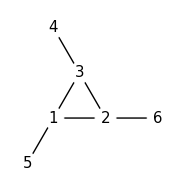
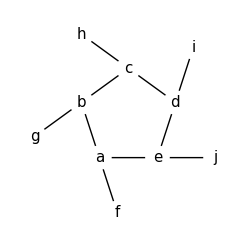
考虑下面这个“魔力”三角形环，在其中填入 1 至 6 这 6 个数，每条线上的三个数加起来都是 9。

					-Graphics-		
从最外侧结点所填的数最小的线（在这个例子中是 4,3,2）开始，按顺时针方向，每个解都能被唯一表述。例如，上面这个解可以记作解集：4,3,2; 6,2,1; 5,1,3。
将环填满后，每条线上的总和一共有四种可能：9, 10, 11 和 12。总共有 8 种填法：
		总和 | 解集
9 | 4,2,3;5,3,1;6,1,2
9 | 4,3,2;6,2,1;5,1,3
10 | 2,3,5;4,5,1;6,1,3
10 | 2,5,3;6,3,1;4,1,5
11 | 1,4,6;3,6,2;5,2,4
11 | 1,6,4;5,4,2;3,2,6
12 | 1,5,6;2,6,4;3,4,5
12 | 1,6,5;3,5,4;2,4,6
把解集中的数字连接起来，可以构造一个 9 位数字串；对于三角形环来说，最大的数字串是 432621513。
在如下的“魔力”五边形环中，在其中填入 1 至 10 这 10 个数，根据不同的填写方式，可以组成 16 位或 17 位数字串。在“魔力”五边形环中，最大的 16 位数字串是多少？
				-Graphics-

```mathematica
Block[{a,b,c,d,e,f,g,h,i,j},
  a = {0, 0};
  b = {-Cos[72°], Sin[72°]};
  c = {1/2, Sin[72°]+Sin[36°]};
  d = {1+Cos[72°], Sin[72°]};
  e = {1, 0};
  f = {Cos[72°], -Sin[72°]};
  g = {-Cos[72°]-Cos[36°], Sin[72°]-Sin[36°]};
  h = {1+Cos[72°]-2Cos[36°], Sin[72°]+2Sin[36°]};
  i = {1+2Cos[72°], 2Sin[72°]};
  j = {2, 0};
  Graphics[{
    Line[{a,b,c,d,e,a}],
    Line[{a,f}], Line[{b,g}], Line[{c,h}], Line[{d,i}], Line[{e,j}],
    EdgeForm[Thickness[0.004]],LightGray,
    Map[Disk[#,0.2]&, {a,b,c,d,e,f,g,h,i,j}],
    Black,
    Map[Inset[Style[#,15],Symbol[#]]&, CharacterRange["a","j"]]
  },ImageSize->{240, Automatic}]
]
```

```mathematica
Module[{solve,solution,decode,constraint,a,b,c,d,e,f,g,h,i,j},
    solve[total_]:=
        Solve[{
            h+c+d==i+d+e==j+e+a==f+a+b==g+b+c==total,
            1≤{a,b,c,d,e,f,g,h,i,j}≤10
        },{a,b,c,d,e,f,g,h,i,j},Integers];
    
    decode[{}]=Nothing;
    decode[sol_]:=
        FromDigits[{h,c,d,i,d,e,j,e,a,f,a,b,g,b,c}/.sol/. 10->Sequence[1,0]];
    constraint[sol_]:= 
        DuplicateFreeQ[sol]&&
        sol[h]<Min[sol[i],sol[j],sol[f],sol[g]]&&
        Max[sol[a],sol[b],sol[c],sol[d],sol[e]]≠10;
    solution[total_]:= Map[decode]@Select[constraint@*Association]@solve[total];

    Max@ParallelMap[solution,Range[14,19]]
]//Timed
```

6531031914842725
Time: 1.66168

#### 69 欧拉总计函数与最大值

在小于 n 的数中，与 n 互质的数的数目记为欧拉总计函数 φ(n)（有时也称为 φ 函数）。例如，因为 1, 2, 4, 5, 7 和 8 均小于 9 且与 9 互质，故 φ(9)=6。
		n | 互质的数 | φ(n) | n/φ(n)
2 | 1 | 1 | 2
3 | 1,2 | 2 | 1.5
4 | 1,3 | 2 | 2
5 | 1,2,3,4 | 4 | 1.25
6 | 1,5 | 2 | 3
7 | 1,2,3,4,5,6 | 6 | 1.1666...
8 | 1,3,5,7 | 4 | 2
9 | 1,2,4,5,7,8 | 6 | 1.5
10 | 1,3,7,9 | 4 | 2.5
可以看出，对于 n≤10，当 n=6 时 n/φ(n) 取得最大值。
当 n≤1000000 时，求使得 n/φ(n) 取得最大值的 n。

```mathematica
MaximalBy[#/EulerPhi[#]&]@Range[1000000]//First
```

510510

#### 70 欧拉总计函数与重排

在小于 n 的数中，与 n 互质的数的数目记为欧拉总计函数 φ(n)（有时也称为 φ 函数）。例如，因为1, 2, 4, 5, 7 和 8 均小于 9 且与 9 互质，故 φ(9)=6。1 被认为和任意正整数互质，所以 φ(1)=1。
有趣的是，φ(87109) = 79180，而 79180 恰好是 87109 的一个重排。
在 1<n<107 中，有些 n 满足 φ(n) 是 n 的一个重排，求这些取值中使 n/φ(n)  最小的一个。

```mathematica
First@MinimalBy[#/EulerPhi[#]&]@Flatten@ParallelTable[
    With[{n=Prime[i]Prime[j]},
        If[Sort@IntegerDigits@EulerPhi[n]==Sort@IntegerDigits[n],n,Nothing]],
    {i,169,PrimePi[Sqrt[10^7]]},{j,i+1,PrimePi[10^7/Prime[i]]}
]
```

8319823

#### 71 有序分数

考虑形如 n/d 的分数，其中 n 和 d 均为正整数。如果 n<d 且其最大公约数为 1，则该分数称为最简真分数。如果我们将 d≤8 的最简真分数构成的集合按大小升序列出，我们得到：
		1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8
可以看出 2/5 是 3/7 直接左邻的分数。
将所有 d≤1000000 的最简真分数按大小升序排列，求此时 3/7 直接左邻的分数的分子。

```mathematica
Module[{findNum},
    findNum[t_,bestN_,bestD_,currD_,minD_]:=
        If[currD<minD,
            bestN/bestD,
            With[{currN=Floor[(Numerator[t]*currD-1)/Denominator[t]]},
                If[bestN*currD<currN*bestD,
                    With[{delta=Numerator[t]*currD-Denominator[t]*currN},
                         findNum[t,currN,currD,currD-1,Floor[currD/delta+1]]],
                     findNum[t,bestN,bestD,currD-1,minD]]]];
    findNum[t_,n_]:=findNum[t,0,1,n,1];
    Numerator@findNum[3/7,1000000]
]
```

428570

#### 72 分数计数

考虑形如 n/d 的分数，其中 n 和 d 均为正整数。如果 n<d 且其最大公约数为 1，则该分数称为最简真分数。如果我们将 d≤8 的最简真分数构成的集合按大小升序列出，我们得到：
		1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8
可以看出该集合中共有 21 个元素。
d≤1000000 的最简真分数构成的集合中共有多少个元素？

```mathematica
ParallelSum[EulerPhi[n],{n,2,10^6}]
```

303963552391

#### 73 分数有范围计数

考虑形如 n/d 的分数，其中 n 和 d 均为正整数。如果 n<d 且其最大公约数为 1，则该分数称为最简真分数。如果我们将 d≤8 的最简真分数构成的集合按大小升序列出，我们得到：
		1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8
可以看出在 1/3 和 1/2 之间有 3 个分数。
将 d≤12000 的最简真分数构成的集合排序后，在 1/3 和 1/2 之间有多少个分数？

```mathematica
Module[{min,max},
    min[t_,denom_]:=Ceiling[(Numerator[t]*denom+1)/Denominator[t]];
    max[t_,denom_]:=Floor[(Numerator[t]*denom-1)/Denominator[t]];
    ParallelSum[
        Boole[Denominator[n/d]==d],
        {d,5,12000},
        {n,min[1/3,d],max[1/2,d]}]
]//Timed
```

7295372
Time: 3.75891

#### 74 数字阶乘链

145 之所以广为人知，是因为它的各位数字的阶乘之和恰好等于本身：
		1!+4!+5! =1+24+120=145
而 169 则可能不太为人所知，尽管从 169 开始不断地取各位数字的阶乘之和构成了最长的循环回到 169；事实上，只存在三个这样的循环：
		169→363601→1454→169
871→45361→871
872→45362→871
不难证明，从任意数字出发最终都会陷入循环。例如，
		69→363600→1454→169→363601(→1454)
78→45360→871→45361(→871)
540→145(→145)
从 69 开始可以得到一个拥有五个不重复项的链，但是从一个小于一百万的数出发能够得到的最长的无重复项链包含有 60 项。
从小于一百万的数出发，有多少条链恰好包含有 60 个不重复项？

```mathematica
Module[{chain},
    chain[1|2|145|40585]=1;
    chain[871|872|45361|45362]=2;
    chain[169|36301|1454]=3;
    chain[n_]:=chain[n]=1+chain[Total@Factorial@IntegerDigits[n]];
    ParallelSum[Boole[chain[n]==60],{n,1000000}]
]//Timed
```

402
Time: 2.3712

#### 75 唯一的整数边直角三角形

只能唯一地弯折成整数边直角三角形的电线最短长度是 12 厘米；当然，还有很多长度的电线都只能唯一地弯折成整数边直角三角形，例如：
		12 cm: (3,4,5)
24 cm: (6,8,10)
30 cm: (5,12,13)
36 cm: (9,12,15)
40 cm: (8,15,17)
48 cm: (12,16,20)
相反地，有些长度的电线，比如 20 厘米，不可能弯折成任何整数边直角三角形，而另一些长度则有多个解；例如，120 厘米的电线可以弯折成三个不同的整数边直角三角形。
		120 cm: (30,40,50), (20,48,52), (24,45,51)
记电线长度为 L，对于 L≤1500000，有多少种取值只能唯一地弯折成整数边直角三角形？

```mathematica
Module[{bent,count,limit=1500000},
    bent[_]=0;
    count=0;
    Do[If[CoprimeQ[m,n],
        With[{L=2m(m+n)},
            Do[
                Switch[bent[k],0,count++,1,count--];
                bent[k]=bent[k]+1,
                {k,L,limit,L}]]],
        {m,2,Sqrt[limit/2]},
        {n,BitAnd[m,1]+1,Min[m-1,limit/(2m)-m],2}];
    count
]//Timed
```

161667
Time: 5.18827

#### 76 加和计数

将 5 写成整数的和有6种不同的方式：
	4+1
3+2
3+1+1
2+2+1
2+1+1+1
1+1+1+1+1
将 100 写成整数的和有多少种不同的方式？

```mathematica
PartitionsP[100]-1
```

190569291

#### 77 素数加和

将 10 写成素数的和有 5 种不同的方式：
		7+3
5+5
5+3+2
3+3+2+2
2+2+2+2+2
写成素数的和有超过五千种不同的方式的数最小是多少？

```mathematica
Module[{P},
    P[n_]:=P[2,n];
    P[m_,n_]:=0/;2m>n;
    P[m_,n_]:=P[m,n]=
        Boole@PrimeQ[n-m]+P[m,n-m]+P[NextPrime[m],n];
    NestWhile[#+1&,2,P[#]≤5000&]
]
```

71

#### 78 硬币分拆

记 p(n) 是将 n 枚硬币分拆成堆的不同方式数。例如，五枚硬币有 7 种分拆成堆的不同方式，因此 p(5)=7。
	ooooo
oooo    o
ooo    oo
ooo    o    o
oo    oo    o
oo    o     o    o
o    o    o    o    o
找出使 p(n) 能被一百万整除的最小 n 值。

```mathematica
Module[{p, penta},
    p[0|1]=1;
    
    penta[n_,k_,a_,b_,s_,sum_]/;n≥a:=
        penta[n,k+3,a+k+1,b+k,-s,sum+s*(p[n-a]+p[n-b])];
    penta[n_,k_,a_,b_,s_,sum_]:=
       If[n≥b,sum+s*p[n-b],sum];
    penta[n_]:=Mod[penta[n,4,2,1,1,0],1000000];
    
    NestWhile[#+1&,2,(p[#]=penta[#])≠0&]
] // Timed
```

55374
Time: 34.0769

```mathematica
JavaSolve[78,1000000]//Timed
```

55374
Time: 0.015508

#### 79 密码推断

网上银行常用的一种密保手段是向用户询问密码中的随机三位字符。例如，如果密码是 531278，询问第 2, 3, 5 位字符，正确的回复应当是 317。
在文本文件 keylog.txt 中包含了 50 次成功登陆的正确回复。
假设三个字符总是按顺序询问的，分析这个文本文件，给出这个未知长度的密码最短的一种可能。

```mathematica
With[{keylog=Flatten@ImportResource["p079_keylog.txt","Table"]},
    FromDigits[
        {0,1,2,3,6,7,8,9}//.
        (Union[IntegerDigits[keylog]/.{a_,b_,c_}:>Sequence[{a,b},{a,c},{b,c}]]
        /.{b_,a_}:>({A___,a,B___,b,C___}:>{A,b,B,a,C}))
    ]
]
```

73162890

#### 80 平方根数字展开

众所周知，如果一个自然数的平方根不是整数，那么就一定是无理数。这样的平方根的小数部分是无限不循环的。
2 的平方根为 1.41421356237309504880...，它的小数点后一百位数字的和是 475。
对于前一百个自然数，求所有无理数平方根小数点后一百位数字的总和。

```mathematica
Module[{countDigits},
    countDigits[_?(IntegerQ@*Sqrt)]:=0;
    countDigits[x_]:=Total@First@RealDigits[Sqrt[x],10,100];
    Sum[countDigits[x],{x,100}]
]
```

40886

#### 81 路径和：两个方向

在如下的 5 乘 5 矩阵中，从左上方到右下方始终只向右或向下移动的最小路径和为 2427，由标注红色的路径给出。
			(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 954 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)
在这个 31K 的文本文件 matrix.txt 中包含了一个 80 乘 80 的矩阵，求出从该矩阵的左上方到右下方始终只向右和向下移动的最小路径和。

```mathematica
Module[{matrix, dim, route},
    matrix=ImportResource["p081_matrix.txt","CSV"];
    dim=Dimensions[matrix];
    
    route[row_,col_]:=route[row,col]=
        If[{row,col}==dim,
            matrix⟦row,col⟧,
            With[{
                down=If[row<dim⟦1⟧,route[row+1,col],Infinity],
                right=If[col<dim⟦2⟧,route[row,col+1],Infinity]
            }, matrix⟦row,col⟧+Min[down,right]]];
    route[1,1]
]
```

427337

#### 82 路径和：三个方向

在如下的 5 乘 5 矩阵中，从最左栏任意一格出发，始终只向右、向上或向下移动，到最右栏任意一格结束的最小路径和为 994，由标注红色的路径给出。
			(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 954 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)
在这个 31K 的文本文件 matrix.txt 中包含了一个 80 乘 80 的矩阵，求出从最左栏到最右栏的最小路径和。

```mathematica
Module[{matrix, rows, cols, index, unindex,up,down,right,encode,g},
    matrix = ImportResource["p082_matrix.txt", "CSV"];
    {rows, cols}=Dimensions[matrix];
    index[row_,col_]:=(row-1)*rows+col;
    unindex[i_]:=(i-1)~QuotientRemainder~cols+{1,1};

    up[_,{1,_}|{_,cols}]:=Nothing;
    up[weight_,{row_,col_}]:=
        {index[row,col],index[row-1,col]}->weight;
        
    down[_,{rows,_}|{_,cols}]:=Nothing;
    down[weight_,{row_,col_}]:=
        {index[row,col],index[row+1,col]}->weight;
        
    right[_,{_,cols}]:=Nothing;
    right[weight_,{row_,col_}]/;col==cols-1:=
        {index[row,col],index[row,col+1]}->weight+matrix⟦row,col+1⟧;
    right[weight_,{row_,col_}]:=
        {index[row,col],index[row,col+1]}->weight;
        
    encode[x__]:={up[x],down[x],right[x]};

    g=WeightedAdjacencyGraph@SparseArray[
            Flatten@MapIndexed[encode,matrix,{2}],
            {rows*cols,rows*cols},Infinity];

    Min@ParallelMap[
        GraphDistance[g,index[#⟦1⟧,1],index[#⟦2⟧,cols]]&,
        Tuples[Range[rows],{2}]]
]//Timed
```

260324.
Time: 6.31773

#### 83 路径和：四个方向

在如下的 5 乘 5 矩阵中，从左上角到右下角任意地向上、向下、向左或向右移动的最小路径和为 2297，由标注红色的路径给出。
		(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 954 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)
在这个 31K 的文本文件 matrix.txt 中包含了一个 80 乘 80 的矩阵，求出从左上角到右下角任意地向上、向下、向左或向右移动的最小路径和。

```mathematica
Module[{matrix, rows, cols, index, unindex,up,down,left,right,encode,g},
    matrix=ImportResource["p083_matrix.txt","CSV"];
    {rows,cols}=Dimensions[matrix];
    index[row_,col_]:=(row-1)*rows+col;
    unindex[i_]:=(i-1)~QuotientRemainder~cols+{1,1};
    
    up[_,{1,_}]:=Nothing;
    up[weight_,{row_,col_}]:=
        {index[row,col],index[row-1,col]}->weight;
        
    down[_,{rows,_}]:=Nothing;
    down[weight_,{row_,col_}]:=
        {index[row,col],index[row+1,col]}->weight;
        
    left[_,{_,1}]:=Nothing;
    left[weight_,{row_,col_}]:=
        {index[row,col],index[row,col-1]}->weight;
        
    right[_,{_,cols}]:=Nothing;
    right[weight_,{row_,col_}]:=
        {index[row,col],index[row,col+1]}->weight;
        
    encode[x__]:={up[x],down[x],left[x],right[x]};
    
    g=WeightedAdjacencyGraph@SparseArray[
            Flatten@MapIndexed[encode,matrix,{2}],
            {rows*cols,rows*cols},Infinity];
    
    GraphDistance[g,index[1,1],index[rows,cols]]+matrix⟦rows,cols⟧
]
```

425185.

#### 85 数长方形

如果数得足够仔细，能看出在一个 3 乘 2 的长方形网格中包含有 18 个不同大小的长方形，如下图所示：
				-Graphics-
尽管没有一个长方形网格中包含有恰好两百万个长方形，但有许多长方形网格中包含的长方形数目接近两百万，求其中最接近这一数目的长方形网格的面积。

```mathematica
MinimalBy[Last]@
    Map[With[{n=NSolve[#(#+1)n(n+1)/4==2*^6&&n>0,{n}]⟦1,1,2⟧},
        {#*IntegerPart[n],n-IntegerPart[n]}]&,
        Range[50,100]]//First//First
```

2772

#### 86 长方体路径

蜘蛛 S 位于一个 6×5×3 大小的长方体屋子的一角，而苍蝇 F 则恰好位于其对角。沿着屋子的表面，从 S 到 F 的最短.93直线.94距离是 10，路径如下图所示：
				-Graphics3D-
然而，对于任意长方体，“最短”路径实际上一共有三种可能；而且，最短路径的长度也并不一定为整数。
当 M=100 时，若不考虑旋转，所有长、宽、高均不超过 M 且为整数的长方体中，对角的最短距离是整数的恰好有 2060 个；这是使得该数目超过两千的最小 M 值；当 M=99 时，该数目为 1975。
找出使得该数目超过一百万的最小 M 值。

```mathematica
Module[{pythagorean,pyth,triplet,count,path,total},
    (* Generate the table for all Pythagorean triplet *)
    pyth[_]={};
    pythagorean[max_]:=
        Do[If[GCD[m,n]==1,
            With[{a=m^2-n^2,b=2m n},
                If[a>max&&b>max,Break[]];
                pyth[a]=Append[pyth[a],b];
                pyth[b]=Append[pyth[b],a]]],
            {m,Infinity},{n,BitAnd[m,1]+1,m-1,2}];

    (* Find all Pythagorean triplet for the given number *)
    triplet[n_]:=
        Select[0<#<2n&]@Flatten@Map[(n/#)pyth[#]&]@Divisors[n];
        
    (* Count the paths that confirm to the formula a^2+(b+c)^2 for a ≥ b ≥ c> 0 *)
    count[n_][m_]:=If[m>n,Floor[n-m/2]+1,Floor[m/2]];

    (* Count the Pythagorean triplet for the given number *)
    path[n_]:=Total@Map[count[n]]@triplet[n];
        
    (* Count all until total exceeds M *)
    pythagorean[10000];
    total[n_,M_]:=If[M≤0,n-1,total[n+1,M-path[n]]];
    total[1,10^6]
]
```

1818

#### 87 素数幂三元组

最小的可以表示为一个素数的平方，加上一个素数的立方，再加上一个素数的四次方的数是 28。实际上，在小于 50 的数中，一共有 4 个数满足这一性质：
		28=2^2+2^3+2^4
33=3^2+2^3+2^4
49=5^2+2^3+2^4
47=2^2+3^3+2^4
有多少个小于五千万的数，可以表示为一个素数的平方，加上一个素数的立方，再加上一个素数的四次方？

```mathematica
Module[{numbers,count,limit=5*^7},
    numbers[_]=False;
    count=0;
    Do[With[{x=Prime[a]^2+Prime[b]^3+Prime[c]^4},
        If[x<limit&&!numbers[x],numbers[x]=True;count++]],
        {a,1,PrimePi@Sqrt[limit]},
        {b,1,PrimePi@CubeRoot[limit]},
        {c,1,PrimePi@Surd[limit,4]}];
    count
]//Timed
```

1097343
Time: 14.225

#### 88 积和数

若自然数 N 能够同时表示成一组至少两个自然数 {a_(1,)a_2,...,a_k} 的积和和，也即 N = a_1 + a_2 + ... + a_k = a_1 × a_2 × ... × a_k，则 N 被称为积和数。例如，6 是积和数，因为 6 = 1 + 2 + 3 = 1 × 2 × 3。
给定集合的规模 k，我们称满足上述性质的最小 N 值为最小积和数。当 k = 2, 3, 4, 5, 6 时，最小积和数如下所示：
		k=2:4=2×2=2+2
k=3:6=1×2×3=1+2+3
k=4:8=1×1×2×4=1+1+2+4
k=5:8=1×1×2×2×2=1+1+2+2+2
k=6:12=1×1×1×1×2×6=1+1+1+1+2+6
因此，对于 2≤k≤6，所有的最小积和数的和为 4 + 6 + 8 + 12 = 30；注意 8 只被计算了一次。
已知对于 2≤k≤12，所有最小积和数构成的集合是 {4, 6, 8, 12, 15, 16}，这些数的和是 61。
对于 2≤k≤12000，所有最小积和数的和是多少？

```mathematica
Module[{partitions,summations,combine,prodsums,count,limit=12000},
    partitions[x_?PrimeQ]:={{x}};
    partitions[x_]:=partitions[x]=
        With[{f=Divisors[x]⟦2⟧},
            partitions[f,x/f]];

    partitions[f_,x_?PrimeQ]:={{f,x}};
    partitions[f_,x_]:=
        DeleteDuplicates@Map[Sort]@Catenate@Map[combine[f]]@partitions[x];
    
    combine[f_][partition_]:=
        Join[
            MapIndexed[ReplacePart[partition,#2->f#1]&,partition],
            {Prepend[partition,f],{f,Times@@partition}}];
    
    summations[n_]:=
        Map[With[{len=Length[#],sum=Total[#]},
            If[sum≤n,len+n-sum,Nothing]]&,
            partitions[n]];
        
    prodsums[_]=0;
    count=limit;
    Do[
        Scan[
            If[#≤limit&&prodsums[#]==0,
                prodsums[#]=n;
                If[--count==0,Break[]]]&,
            summations[n]],
        {n,2,Infinity}];
        
    Total@DeleteDuplicates@Table[prodsums[k],{k,2,limit}]
]//Timed
```

7587457
Time: 3.25524

#### 89 罗马数字

要正确地用罗马数字表达一个数，必须遵循一些基本规则。尽管符合规则的写法有时会多于一种，但对每个数来说总是存在一种.93最好的.94写法。例如，数 16 就至少有六种写法：

IIIIIIIIIIIIIIII
		VIIIIIIIIIII
		VVIIIIII
		XIIIIII
		VVVI
		XVI

然而，根据规则，只有 XIIIIII 和 XVI 是合理的写法，而后一种因为使用了最少的数字而被认为是最有效的写法。
在这个 11K 的文本文件 roman.txt 中包含了一千个合理的罗马数字写法，但并不都是最有效的写法；有关罗马数字的明确规则，可以参考 关于罗马数字。
求出将这些数都写成最有效的写法所节省的字符数。
注意：你可以假定文件中的所有罗马数字写法都不包含连续超过四个相同字符。

```mathematica
Module[{saved},
    Off[FromRomanNumeral::nrom];
    saved[roman_]:=
        StringLength[roman]-StringLength[RomanNumeral@FromRomanNumeral[roman]];
    Total@Map[saved]@Flatten@ImportResource["p089_roman.txt","Table"]
]
```

743

#### 90 立方体数字对

在一个立方体的六个面上分别标上不同的数字（从 0 到 9），对另一个立方体也如法炮制。将这两个立方体按不同的方向并排摆放，我们可以得到各种各样的两位数。例如，平方数 64 可以通过这样摆放获得：
				-Graphics-
事实上，通过仔细地选择两个立方体上的数字，我们可以摆放出所有小于 100 的平方数：01, 04, 09, 16, 25, 36, 49, 64 和 81。例如，其中一种方式就是在一个立方体上标上 {0, 5, 6, 7, 8, 9}，在另一个立方体上标上 {1, 2, 3, 4, 8, 9}。在这个问题中，我们允许将标有 6 或 9 的面颠倒过来互相表示，只有这样，如 {0, 5, 6, 7, 8, 9} 和 {1, 2, 3, 4, 6, 7} 这样本来无法表示 09 的标法，才能够摆放出全部九个平方数。
在考虑什么是不同的标法时，我们关注的是立方体上有哪些数字，而不关心它们的顺序。
	{1, 2, 3, 4, 5, 6} 等价于 {3, 6, 4, 1, 2, 5}
	{1, 2, 3, 4, 5, 6} 等价于 {1, 2, 3, 4, 5, 9}
但因为我们允许在摆放两位数时将 6 和 9 颠倒过来互相表示，这个例子中的两个不同的集合都可以代表拓展集 {1, 2, 3, 4, 5, 6, 9}。
对这两个立方体有多少中不同的标法可以摆放出所有的平方数？

```mathematica
Module[{cube,pairs,check,combination},
    cube=Subsets[Range[0,9],{6}]/. 9->6;
    pairs=Select[FromDigits[#⟦1⟧]≤FromDigits[#⟦2⟧]&]@Catenate@Outer[List,cube,cube,1];
  check[digits_][{a_,b_}]:=
        AllTrue[digits,
            MemberQ[a,#⟦1⟧]&&MemberQ[b,#⟦2⟧]||
            MemberQ[b,#⟦1⟧]&&MemberQ[a,#⟦2⟧]&];
    combination[numbers_]:=
        With[{digits=Map[PadLeft[IntegerDigits[#],2]&,numbers]/. 9->6},
            Select[pairs,check[digits]]];
    Length@combination[Range[9]^2]
]
```

1217

#### 91 格点直角三角形

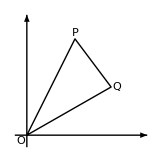
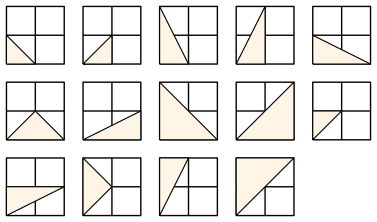
点 P(x_1,y_1) 和点 Q(x_2, y_2) 都是格点，并与原点 O(0,0) 构成 ΔOPQ。
						-Graphics-
当点 P 和点 Q 的所有坐标都在 0 到 2 之间，也就是说 0≤x_1,y_1,x_2,y_2≤2 时，恰好能构造出 14 个直角三角形。
			-Graphics-
如果 0≤x_1,y_1,x_2,y_2≤50，能构造出多少个直角三角形？

```mathematica
With[{MAX=50},
    MAX×MAX+Sum[With[{x1=pts⟦1⟧,y1=pts⟦2⟧,x2=pts⟦3⟧,y2=pts⟦4⟧},
        Boole[x1 y2≠x2 y1 && x1(x2-x1)+y1(y2-y1)==0]],
        {pts,Tuples[Range[0,50],4]}]]
```

14234

MAX×MAX 是所有直角在原点的三角形数目。
x_1 y_2≠x_2 y_1 保证三角形不会退化成一条直线。
x_1(x_2-x_1)+y_1(y_2-y_1)=0 检查直角在点 (x_1,y_1) 的三角形。

#### 92 平方数字链

将一个数的所有数字的平方相加得到一个新的数，不断重复直到新的数已经出现过为止，这构成了一条数字链。例如，
	44→32→13→10→1→1
85→89→145→42→20→4→16→37→58→89
可见，任何一个到达 1 或 89 的数字链都会陷入无尽的循环。更令人惊奇的是，从任意数开始，最终都会到达 1 或 89。
有多少个小于一千万的数最终会到达 89？

```mathematica
Module[{d},
    d[1]=1;
    d[89]=89;
    d[n_]:=d[n]=d[Total[IntegerDigits[n]^2]];
    ParallelSum[Boole[d[n]==89],{n,10^7}]
]//Timed
```

8581146
Time: 14.0172

#### 93 算术表达式

使用集合 {1, 2, 3, 4} 中每个数字恰好一次以及 (+, −, *, /) 四则运算和括号，可以得到不同的正整数。例如，

8 = (4 * (1 + 3)) / 2
		14 = 4 * (3 + 1 / 2)
		19 = 4 * (2 + 3) − 1
		36 = 3 * 4 * (2 + 1)

注意不允许直接把数字连起来，如 12 + 34。
使用集合 {1, 2, 3, 4}，可以得到 31 个不同的数，其中最大值是 36，以及 1 到 28 之间所有的数。
若使用包含有四个不同数字 a<b<c<d 的集合可以得到从 1 到 n 之间所有的数，求其中使得 n 最大的集合，并将你的答案写成字符串：abcd。

```mathematica
Module[{calc,operators,operands,optable,comb,consecutives},
    calc[{p1_,p2_,p3_},{{{a_,b_},c_},d_}]:=p1[p2[p3[a,b],c],d];
    calc[{p1_,p2_,p3_},{a_,{{b_,c_},d_}}]:=p1[a,p2[p3[b,c],d]];
    calc[{p1_,p2_,p3_},{{a_,{b_,c_}},d_}]:=p1[p2[a,p3[b,c]],d];
    calc[{p1_,p2_,p3_},{a_,{b_,{c_,d_}}}]:=p1[a,p2[b,p3[c,d]]];
    calc[{p1_,p2_,p3_},{{a_,b_},{c_,d_}}]:=p1[p2[a,b],p3[c,d]];

    operators=Tuples[{Plus,Subtract,Times,Divide},3];
    operands=Catenate@Map[Groupings[#,2]&]@Permutations[{"a","b","c","d"}];
    optable=DeleteDuplicates@Catenate@Outer[calc,operators,operands,1];

    comb[{a_,b_,c_,d_}]:=With[{r={"a"->a,"b"->b,"c"->c,"d"->d}},
        DeleteDuplicates@Map[
            With[{x=Quiet@Check[#/.r,Infinity]},
                If[IntegerQ[x]&&Positive[x],x,Nothing]]&,
            optable]];
    
    consecutives[seq_]:=Count[0]@(Sort[seq]-Range[Length[seq]]);
    FromDigits@First@MaximalBy[consecutives@*comb]@Subsets[Range[9],{4}]
]
```

1258

#### 94 近等边三角形

可以证明，不存在边长为整数的等边三角形其面积也是整数。但是，存在近等边三角形 5-5-6，其面积恰好为 12。我们定义近等边三角形是有两条边一样长，且第三边与这两边最多相差 1 的三角形。
对于所有边长和面积均为整数且周长不超过十亿 (1,000,000,000) 的三角形，求其中近等边三角形的周长之和。

```mathematica
Module[{accum},
    accum[x_,y_,sum_]:=
        With[{s=If[Divisible[2x+1,3],2x+2,2x-2]},
            If[s>10^9,sum,accum[2x+3y,2y+x,s+sum]]];
    accum[7,4,0]
]
```

518408346

三角形面积可由海伦公式求得：
		A=√(s(s-a)(s-b)(s-c))，其中 s=(a+b+c)/2.
将 b=a,c=a±1 代入，得到

A=1/4 (a±1) √((2 a)^2-(a±1)^2)

要使 A 为整数，可设  (2a)^2-(a±1)^2=k^2 ，并将其改写成如下形式：

((3a±1)/2)^2-3(k/2)^2=1

则此问题可以转化为求佩尔方程 x^2-3 y^2=1 的正整数解。已知该方程的最小解为 x_1=2,y_1=1, 其它解可通过以下递归过程求得：
		x_(k+1)=x_1 x_k+n y_1 y_k=2 x_k+3 y_k
y_(k+1)=x_1 y_k+y_1 x_k=2 y_k+x_k
对每一个解 (x,y)，可求得三角形两等边的边长为 a=(2x±1)/3，三角形周长则为 s=3a±1=2x±2.
注意对第一个解 (x_1,y_1)=(2,1) 所得到的三角形是 (1,1,0)，这是无效的，因此要从第二个解 (x_2,y_2)=(7,4) 开始计算。

#### 95 亲和数链

一个数除了本身之外的因数称为真因数。例如，28 的真因数是 1, 2, 4, 7 和 14。这些真因数的和恰好为 28，因此我们称 28 是完全数。
有趣的是，220 的真因数之和是 284，同时 284 的真因数之和是 220，构成了一个长度为 2 的链，我们也称之为亲和数对。
有一些更长的序列并不太为人所知。例如，从 12496 出发，可以构成一个长度为 5 的链：
		12496→14288→15472→14536→14264(→12496→...)
由于这条链最后又回到了起点，我们称之为亲和数链。
找出所有元素都不超过一百万的亲和数链中最长的那条，并给出其中最小的那个数。

```mathematica
Module[{divsum,chain,minval,L=1,maxlen=0,sol=0,LIMIT=10^6},
    divsum[n_]:=DivisorSigma[1,n]-n;

    minval[a_]:=minval[a,divsum[a],a];
    minval[a_,a_,m_]:=m;
    minval[a_,n_,m_]:=minval[a,divsum[n],Min[m,n]];
    
    chain[_]=0;
    Do[If[chain[i]==0,
        With[{nx=NestWhile[(chain[#]=L++;divsum[#])&,i,#≤LIMIT&&chain[#]==0&]},
            If[nx≤LIMIT&&chain[nx]≥chain[i]&&L-chain[nx]>maxlen,
                maxlen=L-chain[nx];
                sol=minval[nx]]]],
        {i,3,LIMIT}];
    sol
]//Timed
```

14316
Time: 19.0777

```mathematica
JavaSolve[95,10^6]//Timed
```

14316
Time: 0.033478

#### 96 数独

数独是一种热门的谜题。它的起源已不可考，但是与欧拉发明的一种类似而更加困难的谜题拉丁方阵之间有着千丝万缕的联系。数独的目标是替换掉 9 乘 9 网格中的空白位置（或 0），使得每行、每列以及每个九宫格中恰好都包含数字 1~9。如下是一个典型的数独谜题以及它的解答。
			0 | 0 | 3 | 0 | 2 | 0 | 6 | 0 | 0
9 | 0 | 0 | 3 | 0 | 5 | 0 | 0 | 1
0 | 0 | 1 | 8 | 0 | 6 | 4 | 0 | 0
0 | 0 | 8 | 1 | 0 | 2 | 9 | 0 | 0
7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 6 | 7 | 0 | 8 | 2 | 0 | 0
0 | 0 | 2 | 6 | 0 | 9 | 5 | 0 | 0
8 | 0 | 0 | 2 | 0 | 3 | 0 | 0 | 9
0 | 0 | 5 | 0 | 1 | 0 | 3 | 0 | 0		4 | 8 | 3 | 9 | 2 | 1 | 6 | 5 | 7
9 | 6 | 7 | 3 | 4 | 5 | 8 | 2 | 1
2 | 5 | 1 | 8 | 7 | 6 | 4 | 9 | 3
5 | 4 | 8 | 1 | 3 | 2 | 9 | 7 | 6
7 | 2 | 9 | 5 | 6 | 4 | 1 | 3 | 8
1 | 3 | 6 | 7 | 9 | 8 | 2 | 4 | 5
3 | 7 | 2 | 6 | 8 | 9 | 5 | 1 | 4
8 | 1 | 4 | 2 | 5 | 3 | 7 | 6 | 9
6 | 9 | 5 | 4 | 1 | 7 | 3 | 8 | 2
一个构造精良的数独谜题应该包含有唯一解，且能够通过逻辑推断来解决，尽管有时可能必须通过“猜测并检验”来排除一些选项（这一要求目前还颇受争议）。寻找答案的复杂度决定了题目的难度；上面这个谜题被认为是简单的谜题，因为我们可以通过直截了当的演绎推理来解决它。
在这个 6K 的文本文件 sudoku.txt 中包含有 50 个不同难度的数独谜题，但保证它们都只有唯一解（文件中的第一个谜题就是上述样例）。
解开这 50 个谜题，找出每个谜题解答左上角的三个数字并连接起来，给出这些数的和；举例来说，上述样例解答左上角的三个数字连接起来构成的数是 483。

```mathematica
Module[{box,eliminate,solve,puzzles},
    box[grid_,row_,col_]:=
        With[{startRow=Floor[(row-1)/3]*3+1,startCol=Floor[(col-1)/3]*3+1},
            Flatten@grid⟦startRow;;startRow+2,startCol;;startCol+2⟧];
    
    eliminate[grid_,row_,col_]:=
        Range[9]~Complement~grid⟦row⟧
                          ~Complement~grid⟦All,col⟧
                          ~Complement~box[grid,row,col];
    
    solve[grid_]:=solve[grid,1,1];
    solve[grid_,10,1]:=grid;
    solve[grid_,row_,10]:=solve[grid,row+1,1];
    solve[grid_,row_,col_]:=solve[grid,row,col+1]/;grid⟦row,col⟧≠0;
    solve[grid_,row_,col_]:=
        Scan[
            With[{result=solve[ReplacePart[grid,{row,col}->#],row,col+1]},
                If[result=!=Null,Return[result]]]&,
            eliminate[grid,row,col]];
    
    puzzles=
        Partition[
            Map[PadLeft[IntegerDigits[#],9]&]@
                Flatten@DeleteCases[{"Grid",_}]@
                    ImportResource["p096_sudoku.txt","Table"],
            9];
    
    Total@ParallelMap[FromDigits[solve[#]⟦1,1;;3⟧]&,puzzles]
]//Timed
```

24702
Time: 14.3613

#### 97 非梅森大素数

1999 年人们发现了第一个超过一百万位的素数，这是一个梅森素数，可以表示为 2^6972593-1，包含有 2,098,960 位数字。在此之后，更多形如 2^p-1 的梅森素数被发现，其位数也越来越多。然而，在 2004 年，人们发现了一个巨大的非梅森素数，包含有 2,357,207 位数字：28433×2^7830457+1。
找出这个素数的最后十位数字。

```mathematica
Mod[28433×PowerMod[2,7830457,10^10],10^10]
```

8739992576

#### 98 重排平方数

将单词 CARE 中的四个字母依次赋值为 1, 2, 9, 6，我们得到了一个平方数：1296=36^2。神奇的是，使用同样的数字赋值，重排后的单词 RACE 同样构成了一个平方数：9216=96^2。我们称 CARE 和 RACE 为重排平方单词对，同时规定这样的单词对不允许有前导零或是不同的字母赋相同的值。
在这个 16K 的文本文件 words.txt 中包含了将近两千个常见英文单词，找出所有的重排平方单词对（一个回文单词不视为它自己的重排）。
重排平方单词对所给出的最大平方数是多少？
注意：所有的重排单词必须出现在给定的文本文件中。

```mathematica
Module[{words,squares,replaceable,squarePair,compareList,anagram},
    words=Map[ToCharacterCode]@Flatten@ImportResource["p098_words.txt","CSV"];
    
    squares[n_]:=squares[n]=
        Table[IntegerDigits[i^2],{i,Floor@Sqrt[10^n-1],Ceiling@Sqrt[10^(n-1)],-1}];
        
    replaceable[code_,value_]:=
        With[{rule=DeleteDuplicates@Thread[code->value]},
            DuplicateFreeQ[rule⟦All,1⟧]&&DuplicateFreeQ[rule⟦All,2⟧]];
    
    squarePair[x_,y_]:=
        With[{sqs=squares[Length[x]]},
            SelectFirst[sqs,replaceable[x,#]&&MemberQ[sqs,y/.Thread[x->#]]&,Nothing]];
    
    compareList[{},{}]=0;
    compareList[{},{__}]=-1;
    compareList[{__},{}]=1;
    compareList[{a_,as___},{a_,bs___}]:=compareList[{as},{bs}];
    compareList[{a_,___},{b_,___}]:=a-b;
    
    anagram[word_]:=With[{w=Sort[word]},
        Map[If[compareList[word,#]>0&&Sort[#]==w,
                squarePair[word,#],
                Nothing]&,
            words]];
        
    Max@Map[FromDigits]@Catenate@ParallelMap[anagram,words]
]//Timed
```

18769
Time: 4.30109

#### 99 最大的幂

比较两个如 2^11 和 3^7 这样写成幂的形式的数并不困难，任何计算器都能验证 2^11 = 2048 < 3^7 = 2187。然而，想要验证 632382^518061 > 519432^525806 就会变得非常困难，因为这两个数都包含有超过三百万位数字。
22K 的文本文件 base_exp.txt 有一千行，每一行有一对底数和指数，找出哪一行给出的幂的值最大。
注意：文件的前两行就是上述两个例子。

```mathematica
First@First@MaximalBy[Last]@
    MapIndexed[#2⟦1⟧->N[#1⟦2⟧Log[#1⟦1⟧]]&]@
        ImportResource["p099_base_exp.txt","CSV"]
```

709

#### 100 安排概率

在一个盒子中装有 21 个彩色碟子，其中 15 个是蓝的，6 个是红的。如果随机地从盒子中取出两个碟子，取出两个蓝色碟子的概率是 P(BB) = (15 / 21) × (14 / 20) = 1 / 2。下一组使得取出两个蓝色盘子的概率恰好为 50% 的安排，是在盒子中装有 85 个蓝色碟子和 35 个红色碟子。
当盒子中装有超过 10^12=1000000000000 个碟子时，找出第一组满足上述要求的安排，并求此时盒子中蓝色碟子的数量。

```mathematica
Solve[(b(b-1))/(n(n-1))==1/2&&0<b<10^12<n,{b,n},Integers]
```

{{b→756872327473,n→1070379110497}}

#### 101 最优多项式

如果我们知道了一个数列的前 k 项，我们仍无法确定地给出下一项的值，因为有无穷个多项式生成函数都有可能是这个数列的模型。例如，让我们考虑立方数的序列，它可以用如下函数生成，
		u_n=n^3:1,8,27,64,125,216,...
如果我们只知道数列的前两项，秉承“简单至上”的原则，我们应当假定这个数列遵循线性关系，并且预测下一项为 15（公差为 7）。即使我们知道了数列的前三项，根据同样的原则，我们也应当首先假定数列遵循二次函数关系。一般地，给定数列的前 k 项，定义 OP(k,n) 是由最优多项式生成函数给出的第 n 项的值。显然 OP(k,n) 可以精确地给出 n≤k 的那些项，而可能的第一个不正确项将会是 OP(k,k+1)；如果事实的确如此，我们称这个多项式为坏最优多项式。在最基本的情况下，如果我们只得到了数列的第一项，我们应当假定数列为常数，也就是说，对于 n≥2，OP(1,n)=u_1。由此，我们得到了立方数列的最优多项式如下：
		OP(1,n)=1 | 1,1,1,1,...
OP(2,n)=7n-6 | 1,8,15,...
OP(3,n)=6 n^2-11n+6 | 1,8,27,58,...
OP(4,n)=n^3 | 1,8,27,64,125,...
显然，当 k≥4 时不存在坏最优多项式。所有坏最优多项式的第一个不正确项（用红色标示的数）之和为 1 + 15 + 58 = 74。
考虑下面这个十阶多项式生成函数：
		u_n=1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10
求其所有坏最优多项式的第一个不正确项之和。

```mathematica
Module[{u,OP},
    u[n_]:=1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10;
    OP[k_]:=Block[{x},InterpolatingPolynomial[Array[u,k],x]/.x->k+1];
    Sum[OP[k],{k,1,10}]
]
```

37076114526

#### 102 包含原点的三角形

从笛卡尔平面中随机选择三个不同的点，其坐标均满足 -1000≤x,y≤1000，这三个点构成一个三角形。
考虑下面两个三角形：
		A(-340,495),B(-153,-910),C(835,-947)
X(-175,41),Y(-421,-714),Z(574,-645)
可以验证三角形 ABC 包含原点，而三角形 XYZ 不包含原点。
在 27K 的文本文件 triangles.txt 中包含了一千个.93随机.94三角形的坐标，找出其中包含原点在其内部的三角形的数量。
注意：文件中的前两个三角形就是上述样例。

```mathematica
Length@Select[{0,0}∈Triangle@Partition[#,2]&]@
    ImportResource["p102_triangles.txt","CSV"]
```

228

#### 103 特殊的子集和：最优解

记 S(A) 是大小为 n 的集合 A 中所有元素的和。若任取 A 的任意两个非空且不相交的子集 B 和 C 都满足下列条件，我们称 A 是一个特殊的和集：
	i.   S(B) ≠ S(C); 也就是说，任意子集的和不相同。
	ii.  如果 B 中的元素比 C 多，则 S(B) > S(C).
对于给定的 n，我们称使得 S(A) 最小的集合 A 为最优特殊和集。前 5 个最优特殊和集如下所示。
	n=1:{1}
n=2:{1,2}
n=3:{2,3,4}
n=4:{3,5,6,7}
n=5:{6,9,11,12,13}
似乎对于一个给定的最优特殊和集 A = {a_1, a_2, ..., a_n} ，下一个最优特殊和集将是 B = {b, a_1+b, a_2+b, ..., a_n+b} 的形式，其中 b 是集合 A “正中间”的元素。应用这条“规则”，我们猜测对于 n=6 的最优特殊和集将是 A = {11, 17, 20, 22, 23, 24}，相应的 S(A) = 117。然而，事实并非如此，我们的方法仅仅只能找出近似最优特殊和集。对于 n=6，最优特殊和集是 A = {11, 18, 19, 20, 22, 25}，相应的 S(A) = 115，对应的集合数字串是：111819202225。
若集合 A 是 n=7 时的最优特殊和集，求其对应的集合数字串。
注意：此题和 第105题 及 第106题 有关。

```mathematica
FromDigits@Flatten@IntegerDigits[20+{0,11,18,19,20,22,25}] (*cheat*)
```

20313839404245

#### 104 两端为全数字的斐波那契数

斐波那契数列由如下递归关系生成：
		F_n=F_(n-1)+F_(n-2), 其中 F_1=1 且 F_2=1.
可以发现，包含有 113 位数字的 F_541 是第一个后 9 位数字是 1 至 9 全数字（包含 1 至 9 所有的数字，但不一定按照从小到大的顺序）的斐波那契数，而包含有 575 位数字的 F_2749 是第一个前 9 位数字是 1 至 9 全数字的斐波那契数。
若 F_k 是第一个前 9 位数字和后 9 位数字都是 1 至 9 全数字的斐波那契数，求 k。

```mathematica
Module[{pandigitalQ,search},
    pandigitalQ[digits_List]:=Sort[digits]==Range[9];
    search[a_,b_,n_]:=
        If[pandigitalQ@IntegerDigits[a] && pandigitalQ@Take[IntegerDigits@Fibonacci[n],9],
            n,
            search[b,Mod[a+b,10^9],n+1]];
    Block[{$IterationLimit=Infinity},search[1,1,1]]
]//Timed
```

329468
Time: 2.0706

#### 105 特殊的子集和：检验

记 S(A) 是大小为 n 的集合 A 中所有元素的和。若任取 A 的任意两个非空且不相交的子集 B 和 C 都满足下列条件，我们称 A 是一个特殊的和集：
	i.   S(B) ≠ S(C); 也就是说，任意子集的和不相同。
	ii.  如果 B 中的元素比 C 多，则 S(B) > S(C).
例如，{81, 88, 75, 42, 87, 84, 86, 65} 不是一个特殊和集，因为 65 + 87 + 88 = 75 + 81 + 84，而 {157, 150, 164, 119, 79, 159, 161, 139, 158} 满足上述规则，且相应的 S(A) = 1286。
在 4K 的文本文件 sets.txt 中包含了一百组包含 7 至 12 个元素的集合（文档中的前两个例子就是上述样例），找出其中所有的特殊和集 A_1,A_2,...,A_k，并求 S(A_1)+S(A_2)+...+S(A_k) 的值。
注意：此题和 第103题 及 第106题 有关。

```mathematica
Module[{rule1,rule2,specialSetQ},
    rule1[set_]:=DuplicateFreeQ[Plus@@@Subsets[set,{1,Length[set]-1}]];
    
    rule2[set_]:=rule2[Sort[set],2,1];
    rule2[set_,i_,j_]:=True/;i+j>Length[set];
    rule2[set_,i_,j_]:=
        If[Plus@@Take[set,i]≤Plus@@Take[set,-j],False,
            rule2[set,i+1,j+1]];
    
    specialSetQ[s_]:=rule2[s]&&rule1[s];
    Total[Plus@@@Select[specialSetQ]@ImportResource["0105_sets.txt","CSV"]]
]
```

73702

#### 106 特殊的子集和：元检验

记 S(A) 是大小为 n 的集合 A 中所有元素的和。若任取 A 的任意两个非空且不相交的子集 B 和 C 都满足下列条件，我们称 A 是一个特殊的和集：
	i.   S(B) ≠ S(C); 也就是说，任意子集的和不相同。
	ii.  如果 B 中的元素比 C 多，则 S(B) > S(C).
在这个问题中我们假定集合中包含有 n 个严格单调递增的元素，并且已知其满足第二个条件。
令人惊奇的是，当 n=4 时，在所有可能的 25 组子集对中只有 1 组需要检验子集和是否相等（第一个条件）。同样地，当 n=7 时，在所有可能的 966 组子集对中只有 70 组需要检验。
当 n=12 时，在所有可能的 261625 组子集对中有多少组需要检验？
注意：此题和 第103题 及 第105题 有关。

```mathematica
With[{n=12},
    ∑_(k=2)^(n/2) (1/2 Binomial[n, k] Binomial[n-k, k]-k Binomial[n, 2 k])
]
```

21384

#### 107 最小网络

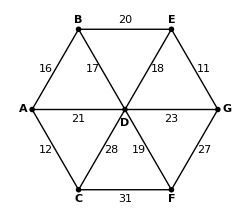
下面这个无向网络包含有 7 个顶点和 12 条边，其总权重为 243。
		-Graphics-
这个网络也可以用矩阵的形式表示如下。
		  | A | B | C | D | E | F | G
A | - | 16 | 12 | 21 | - | - | -
B | 16 | - | - | 17 | 20 | - | -
C | 12 | - | - | 18 | - | 31 | -
D | 21 | 17 | 28 | - | 18 | 19 | 23
E | - | 20 | - | 18 | - | - | 11
F | - | - | 31 | 19 | - | - | 27
G | - | - | - | 23 | 11 | 27 | -
然而，我们其实可以优化这个网络，移除其中的一些边，同时仍然保证每个顶点之间都是连通的。节省权重最多的网络如下图所示，其总权重为 93，相比原来的网络节省了 243 - 93 = 150。
		-Graphics-
在这个 6K 的文本文件 network.txt 中存放了一个包含有 40 个顶点的网络的连通矩阵。移除其中冗余的边，同时仍然保证每个顶点之间都是连通的，求最多能节省的权重。

```mathematica
With[{
    network=WeightedAdjacencyGraph[
        ImportResource["0107_network.txt","CSV"]/."-"->Infinity]},
    Total@Map[PropertyValue[{network,#},EdgeWeight]&]@
        EdgeList@GraphDifference[network,FindSpanningTree[network]]
]
```

259679

#### 108 倒数丢番图方程（一）

在如下方程中，x,y,n 均为正整数。
		1/x+1/y=1/n
对于 n=4，上述方程恰好有 3 个不同的解：
		1/5+1/20=1/4
1/6+1/12=1/4
1/8+1/8=1/4
使得不同的解的数目超过 1000 的最小 n 值是多少？
注意：这个问题是 第110题 的简单版本；强烈推荐先解决这一题。

```mathematica
With[{limit=1000},
    With[{step=Function[If[#1#2>limit,#1,#0[#1#2,NextPrime[#2]]]][1,2]},
        NestWhile[#+step&,step,DivisorSigma[0,#^2]<2limit-1&]]]
```

180180

将方程改写为 y=xn/(x-n). 可知当 n+1≤x≤2n 且 xn∣(x-n) 时，能得到 x,y 的所有正整数解。不妨设 x=n+m，其中 1≤m≤n，再将方程改写为 y=n+n^2/m. 即可看出答案就是在区间 [1..n] 中能整除 n^2 的除数的个数。

#### 109 飞镖

在飞镖游戏中，玩家需向靶子上投掷三枚飞镖；靶子被分成了二十个相等面积的区域，并分别标上 1 至 20。
		-Graphics-
每一枚飞镖的分数还取决于它的位置。落在外围的红/绿色圈以外时为零分，落在黑/白色区域时为一倍得分，而落在外围和中间的红/绿色圈时分别为两倍和三倍得分。在把子的正中心有两个同心圆，被称为靶心。射中靶心外圈得 25 分，射中靶心内圈则得双倍 50 分。
飞镖的规则有许多变种，但最热门的一种是，每个玩家从 301 分或 501 分开始，轮流投掷飞镖并减去得分，首先将自己的分数减少到恰好为 0 的玩家获胜。不过，通常会采用“双倍结束”规则，即玩家在最后一镖必须射中一个双倍区域（包括双倍的靶心内圈）才能判定获胜。若这一轮的得分使得玩家的分数减少到 1 分或更少，但最后一镖未射中双倍区域，则这一轮的得分“作废”。玩家在目前的分数下能够获胜则被称为“结分”。最高的结分为 170: T20 T20 D25（两个三倍 20 分和一个双倍靶心）。
当玩家分数为 6 时，恰好有 11 种结分方式：
		D3 |   |  
D1 | D2 |  
S2 | D2 |  
D2 | D1 |  
S4 | D1 |  
S1 | S1 | D2
S1 | T1 | D1
S1 | S3 | D1
D1 | D1 | D1
D1 | S2 | D1
D2 | S2 | D1
注意 D1 D2 被认为是不同于 D2 D1 的结分方式，因为它们最后的双倍不同。不过，组合 S1 T1 D1 和 T1 S1 D1 就被认为是相同的结分方式。另外，我们在计算组合时，我们不考虑脱靶的情况；例如，D3 和 0 D3 以及 0 0 D3 就是相同的结分方式。
令人惊奇的是一共有 42336 种不同的结分方式。
当玩家分数小于 100 时，一共有多少种不同的结分方式？

```mathematica
Module[{scores,doubles},
    scores=Array[Sequence@@{#,2#,3#}&,20]~Join~{25,50};
    doubles=Array[2#&,20]~Append~50;
    Sum[Total@Map[Length@IntegerPartitions[#,2,scores]&,n-doubles],{n,1,99}]
]
```

38182

#### 110 倒数丢番图方程（二）

在如下方程中，x,y,n 均为正整数。
		1/x+1/y=1/n
可以验证当 n=1260 时，恰好有 113 种不同的解，这也是不同的解的总数超过一百种的最小 n 值。
不同的解的总数超过四百万种的最小 n 值是多少？
注意：这是 第108题 一个极其困难的版本，而且远远超过暴力解法的能力范围，因此需要更加聪明的手段。

```mathematica
Module[{divisors,compose,search,limit=4*^6},
    divisors[{p_,n_}]:=((Times@@Map[2#+1&,p])3^n+1)/2;

    compose[{p_,n_}]:=
        Times@@MapThread[Power,{
            Array[Prime,n+Length[p]],
            Join[p, ConstantArray[1,n]]
        }];

    search[n_]:= search[{{2},n-1}];
    
    search[{p_,0}]:={p,0};

    search[{p_,n_}]/;divisors[{p,n-1}]≥limit:=
        search[{p,n-1}];
    
    search[{{a_},n_}]:=
        If[divisors[{{a+1},n-1}]≥limit && divisors[{{a},n}]>divisors[{{a+1},n-1}],
            search[{{a+1},n-1}],
            search[{{a,2},n-1}]];

    search[p:{{c:PatternSequence[___,b_],a_},n_}]:=
        If[a<b && divisors[{{c,a+1},n-1}]≥limit && divisors[p]>divisors[{{c,a+1},n-1}],
            search[{{c,a+1},n-1}],
            With[{candidate=search[{{c,a,2},n-1}]},
                If[divisors[p]>divisors[candidate],candidate,p]]];

    compose@search[Floor@Log[3,2limit-1]+1]
]
```

9350130049860600

#### 111 有重复数字的素数

考虑一个有重复数字的 4 位素数，显然这 4 个数字不能全都一样：1111 被 11 整除，2222 被 22 整除，依此类推；但是，有 9 个 4 位素数包含有三个一：
		1117, 1151, 1171, 1181, 1511, 1811, 2111, 4111, 8111
我们记 M(n,d) 是 n 位素数中数字 d 重复出现的最多次数，N(n,d) 是这类素数的个数，而 S(n,d) 是这类素数的和。
因此 M(4,1) = 3 是 4 位素数中数字 1 重复出现的最多次数，有 N(4,1) = 9 个这类素数，而它们的和是 S(4,1) = 22275。还能得出，对于 d = 0，在 4 位素数中最多重复出现 M(4,0) = 2 次，但是有 N(4,0) = 13 个这类素数。
同样地，我们可以得到 4 位素数的如下结果。

		Digit,d | M(4,d) | N(4,d) | S(4,d)
0 | 2 | 13 | 67061
1 | 3 | 9 | 22275
2 | 3 | 1 | 2221
3 | 3 | 12 | 46214
4 | 3 | 2 | 8888
5 | 3 | 1 | 5557
6 | 3 | 1 | 6661
7 | 3 | 9 | 57863
8 | 3 | 1 | 8887
9 | 3 | 7 | 48073
对于 d=0 至 9，所有 S(4,d) 的和为 273700。
求所有 S(10,d) 的和。

```mathematica
Module[{insert,run},
    insert[0,n_,m_]/;n==m-1:={};
    insert[a_,n_,m_]/;n==m-1:=
        Select[PrimeQ]@Map[
            FromDigits@Insert[ConstantArray[a,n],Sequence@@#]&,
            Tuples[{DeleteCases[a]@Range[9],Range[m]}]];
    
    insert[a_,n_,m_]:=
        Select[IntegerLength[#]==m&&PrimeQ[#]&]@Map[
            FromDigits@Fold[
                Insert[#1,Sequence@@#2]&,
                ConstantArray[a,n],
                #]&,
            Catenate@Outer[
                Transpose@*List,
                Tuples[DeleteCases[a]@Range[0,9],m-n],
                Subsets[Range[m],{m-n}],
                1]];
    
    run[a_,m_]:=run[a,m-1,m];
    run[a_,n_,m_]:=With[{primes=insert[a,n,m]},
        If[Length[primes]≠0,primes,run[a,n-1,m]]];
    
    Total@Map[Total@run[#,10]&]@Range[0,9]
]
```

612407567715

#### 112 弹跳数

从左往右，如果每一位数字都大于等于其左边的数字，这样的数被称为上升数，比如 134468。同样地，如果每一位数字都大于等于其右边的数字，这样的数被称为下降数，比如 66420。如果一个正整数既不是上升数也不是下降数，我们就称之为“弹跳”数，比如 155349。
显然不存在小于一百的弹跳数，而在小于一千的数中有略超过一半（525）的弹跳数。事实上，使得弹跳数的比例恰好达到 50% 的最小数是 538。令人惊奇的是，弹跳数将变得越来越普遍，到 21780 时，弹跳数的比例恰好等于 90%。
找出使得弹跳数的比例恰好为 99% 的最小数。

```mathematica
Module[{BouncyQ,count},
    BouncyQ[n_]:=With[{digits=IntegerDigits[n]},
        !(OrderedQ[digits]||OrderedQ[digits,GreaterEqual])];
    count=0;
    Do[
        If[(count+=Boole@BouncyQ[n])/n==99/100,Return[n]],
        {n,100,Infinity}]
]//Timed
```

1587000
Time: 10.8079

#### 113 非弹跳数

从左往右，如果每一位数字都大于等于其左边的数字，这样的数被称为上升数，比如 134468。同样地，如果每一位数字都大于等于其右边的数字，这样的数被称为下降数，比如 66420。如果一个正整数既不是上升数也不是下降数，我们就称之为“弹跳”数，比如 155349。随着 n 的增长，小于 n 的弹跳数的比例也随之增长；在小于一百万的数中，只有 12951 个非弹跳数，而小于 10^10 的数中只有 277032 个非弹跳数。
在小于一古戈尔（10^100）的数中有多少个非弹跳数？

```mathematica
Sum[Binomial[n+8,n]+Binomial[n+9,n]-10,{n,1,100}]
```

51161058134250

#### 114 方格组合计数（一）

用黑色方块和最短长度为 3 的红色方块摆成长度为 7 的一行，要求任意两个红色方块（长度可以不同）之间至少有一个黑色方块，恰好有 17 种不同的摆法。
	-Graphics-
若要摆成长度为 50 的一行，有多少种不同的摆法？
注意：尽管上述样例没有混用不同长度的方格，但这样做是允许的。例如，要摆成长度为 8 的一行，你可以用红 (3)、黑 (1)、红 (4)。

```mathematica
Module[{F},
    F[n_]:=0/;n<3;
    F[n_]:=F[n]=Sum[F[n-i-j-1]+1,{i,3,n},{j,0,n-i}];
    F[50]+1
]
```

16475640049

#### 115 方格组合计数（二）

注意：这是 第 114 题 一个更难的版本。
用黑色方块和最短长度为 m 的红色方块摆成长度为 n 的一行，要求任意两个红色方块（长度可以不同）之间至少有一个黑色方块。
我们用摆法计数函数 F(m,n) 代表符合上述要求的摆法数目。
例如，F(3, 29) = 673135 以及 F(3, 30) = 1089155。
也就是说，当 m = 3 时，可以看出 n = 30 是使得摆法计数函数首次超过一百万的最小值。
同样地，当 m = 10 时，可以验证 F(10, 56) = 880711 以及 F(10, 57) = 1148904，因此 n = 57 是使得摆法计数函数首次超过一百万的最小值。
当 m = 50 时，求使得摆法计数函数首次超过一百万的最小 n 值。

```mathematica
Module[{F},
    F[m_,n_]:=0/;n<m;
    F[m_,n_]:=F[m,n]=Sum[F[m,n-i-j-1]+1,{i,m,n},{j,0,n-i}];
    NestWhile[#+1&,1,F[50,#]+1<10^6&]
]
```

168

#### 116 红色、绿色或蓝色的地砖（一）

将一行五块黑色方形地砖的一部分替换成红色（长度为 2）、绿色（长度为 3）或蓝色（长度为 4）的地砖。
如果只使用红色地砖，一共有 7 种不同的替换方式。
	-Graphics-
如果只使用绿色地砖，一共有 3 种不同的替换方式。
	-Graphics-
如果只使用蓝色地砖，一共有 2 种不同的替换方式。
	-Graphics-
假定颜色不能混合使用，一共有 7 + 3 + 2 = 12 种方式替换一行五块黑色地砖。
假定颜色不能混合使用，且至少使用一种彩色地砖，一共有多少种方式替换一行五十块黑色地砖？
注意：这道题与 第 117  题有关。

```mathematica
Module[{F},
    F[m_,n_]:=0/;n<m;
    F[m_,n_]:=F[m,n]=Sum[F[m,n-m-i]+1,{i,0,n-m}];
    F[2,50]+F[3,50]+F[4,50]
]
```

20492570929

#### 117 红色、绿色和蓝色的地砖（二）

使用黑色地砖、长度为 2 的红色地砖、长度为 3 的绿色地砖、长度为 4 的蓝色地砖的组合，一共有恰好 15 种不同的方式铺满长度为5的一行。
	-Graphics-
一共有多少种不同的方式铺满长度为 50 的一行？
注意：这道题和 第 116 题 有关。

```mathematica
Module[{F},
    F[n_]:=0/;n<2;
    F[n_]:=F[n]=Sum[F[n-i-j]+1,{i,2,4},{j,0,n-i}];
    F[50]+1
]
```

100808458960497

#### 118 全数字素数集合

使用 1 至 9 的全部数字，并自由连接起来组成十进制整数，可以构造不同的集合。其中一个集合 {2, 5, 47, 89, 631} 非常有趣，因为它的所有元素都是素数。
有些集合包含数字 1 至 9 恰好各一次，且所有元素都是素数，这样的集合有多少个？

```mathematica
Module[{candidates,candidateGroup,partitions,pandigitalPrimesQ,countPrimes},
    candidates=Counts@ParallelTable[
        With[{digits=IntegerDigits@Prime[i]},
            If[!MemberQ[digits,0]&&DuplicateFreeQ[digits],
                FromDigits@Sort[digits],
                Nothing]],
        {i,1,PrimePi[98765432]}];
    
    candidateGroup[len_]:=candidateGroup[len]=
        Select[IntegerLength[#]==len&]@Keys[candidates];
    
    partitions=DeleteCases[
        Map[Sort]@IntegerPartitions[9],
        {9}|{___,Repeated[1,{5}],___}];
    
    pandigitalPrimesQ[primes_]:=
        DuplicateFreeQ@Flatten@IntegerDigits[primes];
    
    countPrimes[group_]:=countPrimes[group,{}];
    
    countPrimes[{},primes_]:=
        If[pandigitalPrimesQ[primes],
            Times@@Map[candidates,primes],
            0];
    
    countPrimes[{g_,gs___},primes_]:=
        Fold[
            If[Length[primes]==0||#2>Last[primes],
                #1+countPrimes[{gs},Append[primes,#2]],
                #1]&,
            0,candidateGroup[g]];
    
    Plus@@ParallelMap[countPrimes,partitions]
]//Timed
```

44680
Time: 14.4554

```mathematica
JavaSolve[118]//Timed
```

44680
Time: 1.45144

#### 119 数字和的幂

512 是一个有趣的数，因为它等于其各位数字和的幂：5 + 1 + 2 = 8，而 8^3 = 512。拥有同样性质的数的另一个例子是 614656 = 28^4。记 a_n 是这类数中的第 n 个，并且约定一个数至少需要两位数字才有各位数字和。已知 a_2 = 512 以及 a_10 = 614656。
求 a_30。

```mathematica
Module[{fQ},
    fQ[n_]:= With[{b=Total@IntegerDigits[n]},
        If[n<10||b==1,False,IntegerQ@Log[b,n]]];
    (Select[fQ]@Union@Flatten@Table[n^m,{n,2,100},{m,2,10}])⟦30⟧
]
```

248155780267521

#### 120 平方余数

记 r 是 (a-1)^n+(a+1)^n 被 a^2 除所得的余数。
例如，如果 a=7 而 n=3，则 r=42:6^3+8^3=728≡42 mod 49。随着 n 的变化，r 也会随之变化，但是对 a=7，可以得出 r_max=42。
对于 3≤a≤1000，求 ∑r_max。

```mathematica
Sum[2 a Floor[(a-1)/2],{a,3,1000}]
```

333082500

当 n 是偶数时，(a-1)^n+(a+1)^n≡2 mod a^2；当 n 是奇数时，(a-1)^n+(a+1)^n≡2na mod a^2。找出最大的 n 使得 2na<a^2。

#### 121 碟子游戏奖金

一开始，包里装有一个红色碟子和一个蓝色碟子。在一场概率游戏中，每一轮玩家从包中取出一个碟子，记录下其颜色，随后将碟子放回包中，并在包中加入一个红色碟子，再进行下一轮。玩家需要付 £1 来玩这个游戏，如果他们在游戏结束时拿出的蓝色碟子数比红色碟子数更多，则获得胜利。
如果游戏进行 4 轮，那么玩家获胜的概率是 11 / 120，因此游戏所设定的最高奖金为 £10，否则可能会造成亏损。注意奖金必须是整数，而且包含了玩家付出用于玩游戏的 £1，也就是说玩家实际上赢得的数额是 £1。
如果游戏进行 15 轮，求游戏所设定的最高奖金。

```mathematica
Module[{f},
    f[n_]:=Floor[n!/Tr@Abs@Table[StirlingS1[n,i],{i,Ceiling[n/2]+1,n}]];
    f[16]
]
```

2269

#### 122 高效指数计算

计算 n^15 最朴素的方式需要 14 次乘法：
	n×n×...×n=n^15
但使用一个“二进制”的算法，你可以只用 6 次乘法：
	n×n=n^2
	n^2×n^2=n^4
	n^4×n^4=n^8
	n^8×n^4=n^12
	n^12×n^2=n^14
	n^14×n=n^15
然而，实际上仅用 5 次乘法也是可以的：
	n×n=n^2
	n^2×n=n^3
	n^3×n^3=n^6
	n^6×n^6=n^12
	n^12×n^3=n^15
记 m(k) 是计算 n^k 所需要的最少次数，例如 m(15) = 5。
对于 1≤k≤200，求 ∑m(k)。

```mathematica
Total@JavaSolve[122,200]
```

1582

#### 123 素数平方余数

记 p_n 是第 n 个素数：2, 3, 5, 7, 11,...；记 r 是 (p_n-1)^n+(p_n+1)^n 被 p_n^2 除所得的余数。例如，当 n=3 时，p_3=5，而 4^3+6^3=280≡5 mod 25。
使余数首次超过 10^9 的最小 n 值是 7037。
求使余数首次超过 10^10 的最小 n 值。

```mathematica
NestWhile[#+2&,7037,2# Prime[#]<10^10&]
```

21035

提示：当 n 是奇数时，(p_n-1)^n+(p_n+1)^n≡2n p_n mod p_n^2

#### 124 基排序

数 n 的基 rad(n)，是指 n 的不同质因数之积。例如，504 = 2^3 × 3^2 × 7，所以 rad(504) = 2 × 3 × 7 = 42。
如果我们计算 1≤n≤10 的 rad(n)，并先按照 rad(n) 再按照 n 从小到大排序，我们得到：
				排序前
n | rad(n)
1 | 1
2 | 2
3 | 3
4 | 2
5 | 5
6 | 6
7 | 7
8 | 2
9 | 3
10 | 10		排序后
n | rad(n) | k
1 | 1 | 1
2 | 2 | 2
4 | 2 | 3
8 | 2 | 4
3 | 3 | 5
9 | 3 | 6
5 | 5 | 7
6 | 6 | 8
7 | 7 | 9
10 | 10 | 10
记 E(k) 是前 n 个数排序后的第 k 个数，例如，E(4) = 8 以及 E(6) = 9。
对 1≤n≤100000 按照 rad(n) 排序后，求 E(10000)。

```mathematica
With[{rad=Apply[Times]@*Map[First]@*FactorInteger},
    Part[SortBy[rad]@Range[100000],10000]
]
```

21417

#### 125 回文和

回文数 595 很有趣，因为它可以写成连续平方数的和：6^2 + 7^2 + 8^2 + 9^2 + 10^2 + 11^2 + 12^2。恰好有十一个小于一千的回文数可以写成连续平方数的和，这些回文数的和是 4164。注意1 = 0^2 + 1^2 并没有算在内，因为本题只考虑正整数的平方。
在小于10^8 的数中，找出所有可以写成连续平方数的和的回文数，并求它们的和。

```mathematica
Module[{squaresum,table,LIMIT=10^8},
    squaresum[k_,m_]:=k(k+m)(1+m)+m(1+m)(1+2m)/6;
    table={};
    Do[
        Do[
            With[{x=squaresum[k,m]},
                If[x>LIMIT,Break[]];
                If[PalindromeQ[x]&&!MemberQ[table,x],AppendTo[table,x]]],
            {m,1,Infinity}],
        {k,1,Sqrt[LIMIT]}];
    Total[table]
]
```

2906969179

#### 129 循环单位数整除性

只包含数字 1 的数被称为循环单位数，我们定义 R(k) 是长为 k 的循环单位数，例如，R(6) = 111111。
如果 n 是一个整数，且 GCD(n,10)=1，可以验证总存在 k 使得 R(k) 能够被 n 整除，并且记 A(n) 是这些 k 中最小的一个。例如，A(7) = 6，而 A(41)  =  5。
使得 A(n) 第一次超过十的 n 是 17。
求使得 A(n) 第一次超过一千万的 n。

```mathematica
Module[{A,LIMIT=10^6},
    A[n_]:=If[GCD[n,10]≠1,0,MultiplicativeOrder[10,9n]];
    NestWhile[#+2&,LIMIT+1,A[#]<LIMIT&]
]
```

1000023

#### 130 满足素数循环单位数性质的合数

只包含数字 1 的数被称为循环单位数，我们定义 R(k) 是长为 k 的循环单位数，例如，R(6) = 111111。
如果 n 是一个整数，且 GCD(n,10)=1，可以验证总存在 k 使得 R(k) 能够被 n 整除，并且记 A(n) 是这些 k 中最小的一个。例如，A(7) = 6，而 A(41) = 5。已知对于素数 p>5，p−1 能够被 A(p) 整除。例如，当 p=41 时，A(41) = 5，而 40 能够被 5 整除。然而，有很少的一部分合数也满足这条性质，前 5 个这样的数分别是 91, 259, 451, 481 以及 703。
找出前 25 个合数 n 满足 GCD(n,10)=1 且 n−1 能够被 A(n) 整除，并求它们的和。

```mathematica
Module[{A,check,accum},
    check[n_]:=And[
        !PrimeQ[n],
        GCD[n,10]==1,
        Divisible[n-1,MultiplicativeOrder[10,9n]]];
    accum[_,0,s_]:=s;
    accum[n_?check,k_,s_]:=accum[n+2,k-1,s+n];
    accum[n_,k_,s_]:=accum[n+2,k,s];
    Block[{$IterationLimit=Infinity},accum[7,25,0]]
]
```

149253

#### 131 素数立方数组合

对于某些素数 p，存在正整数 n，使得表达式 n^3+n^2 p 是立方数。
例如，对于 p = 19, 8^3+8^2×19=12^3。
非常奇特的是，对于满足这个性质的素数，n 的值都是唯一的。在小于一百的素数中，只有四个素数满足这个性质。
在小于一百万的素数中，有多少个素数满足这个神奇的性质？

```mathematica
With[{LIMIT=10^6},
    Sum[Boole@PrimeQ[3k(k+1)+1],{k,Sqrt[LIMIT/3]}]]
```

173

由等式 n^3+n^2 p≡n^2(n+p) 可知，n 和 n+p 都必须是立方数才能使得 n^3+n^2 p 是立方数，因此 p 必须是两个立方数之差。又由于 x^3-y^3≡(x-y)(x^2+xy+y^2) ，要使两个立方数之差为素数，则要求 x-y=1。由此得到生成立方素数的方程：

p=(y+1)^3-y^3=3 y^2+3y+1,y=1,2,...

#### 132 大循环单位数的因数

只包含数字 1 的数被称为循环单位数，我们定义 R(k) 是长为 k 的循环单位数。例如，R(10) = 1111111111 = 11 × 41 × 271 × 9091，这些质因数的和是 9414。
找出 R(10^9) 的前 40 个质因数的和。

```mathematica
Module[{remainder,accum},
    remainder[n_,k_]:=Mod[PowerMod[10,k,9n]-1,9n];
    accum[_,0,total_]:=total;
    accum[i_,count_,total_]:=
        If[remainder[Prime[i],10^9]==0,
            accum[i+1,count-1,total+Prime[i]],
            accum[i+1,count,total]];
    Block[{$IterationLimit=Infinity},accum[1,40,0]]
]
```

843296

#### 133 循环单位数的非质因数

只包含数字 1 的数被称为循环单位数，我们定义 R(k) 是长为 k 的循环单位数；例如，R(6) = 111111。
考虑形如 R(10^n) 的循环单位数。尽管 R(10), R(100) 和 R(1000) 都不能被 17 整除，R(10000) 却能够被 17 整除。然而，不存在 n 使得 R(10^n) 能被 19 整除。事实上，在小于 100 的质数中，只有 11, 17, 41 和 73 能够成为 R(10^n) 的质因数。
找出所有小于十万且永远不会成为 R(10^n) 的质因数的质数之和。

```mathematica
Module[{q},
    q[k_]:=!(First/@FactorInteger@MultiplicativeOrder[10,9k])~ContainsOnly~{2,5};
    Total@Select[q]@Prime[Range[4,PrimePi[10^5]]]]+2+3+5
```

453647705

#### 134 质数对连接

考虑连续的质数 p_1 = 19 和 p_2 = 23。可以验证，1219 是所有以 p_1 结尾并且能被 p_2 整除的数中最小的一个。
事实上，除了 p_1 = 3 和 p_2 = 5 这一对之外，对于任意一对连续质数 p_2>p_1，都存在一系列的数 n，其尾数是 p_1，且能够被 p_2 整除。记 S 是所有的 n 中的最小值。
对于 5≤p_1≤1000000 内的所有连续质数对，求 ∑S。

```mathematica
Module[{f},
    f[{p1_,p2_}]:=ChineseRemainder[{0,p2-p1},{10^IntegerLength[p1],p2}]+p1;
    Total@ParallelMap[f,Partition[Prime[Range[3,PrimePi[10^6]+1]],2,1]]
]//Timed
```

18613426663617118
Time: 1.61049

#### 135 相同的差

已知正整数 x,y,z 构成等差数列，使得方程 x^2-y^2-z^2=n 有两个解的最小正整数为 n=27：
		34^2-27^2-20^2=12^2-9^2-6^2=27
使得方程有十个解的最小正整数为 n=1155。
在小于一百万的数中，有多少个 n 的取值使得方程恰好有十个不同的解？

```mathematica
Module[{check},
    check[_?PrimeQ]=0;
    check[n_]:=
        Length@Select[With[{x=#,y=n/#},
            Divisible[x+y,4]&&3y>x]&
        ]@Divisors[n];
    ParallelSum[Boole[check[n]==10],{n,7,10^6}]
]//Timed
```

4989
Time: 13.7254

```mathematica
JavaSolve[135,10^6]//Timed
```

4989
Time: 0.137281

#### 136 唯一的差

整数 x,y,z 构成等差数列。取正整数 n = 20，此时方程 x^2-y^2-z^2=n 只有一个解：
		13^2-10^2-7^2=20
事实上，在小于一百的数中，有 25 个 n 的取值使得方程有唯一解。
在小于五千万的数中，有多少个 n 的取值使得方程有唯一解？

```mathematica
With[{n=5*^7},
    PrimePi[n/4]+PrimePi[n/16]+
        Length@Select[Divisible[#+1,4]&]@Prime[Range[1,PrimePi[n]]]
]//Timed
```

2544559
Time: 8.10975

由方程式 (a+b)^2-a^2-(a-b)^2=n 可得 b=(n+a^2)/(4a). 使方程式得到唯一整数解的条件是：
(1) n=4p，其中 p=1 或 p 是奇素数；
(2) n=16p，其中 p=1 或 p 是奇素数；
(3) n=p，其中 p 是素数且 p+1≡0 mod 4.

#### 137 斐波那契金块

考虑无穷级数 A_F(x)=x F_1+x^2 F_2+x^3 F_3+...，其中 F_k 是斐波那契数列的第 k 项：1, 1, 2, 3, 5, 8, ...；该数列由如下方式定义：F_k=F_(k-1)+F_(k-2)，其中 F_1 = 1 且 F_2 = 1。
在这个问题中，我们感兴趣的是那些使得 A_F(x) 为正整数的 x。
其中一个特别的解是：

A_F(1/2)=(1/2)1+(1/2)^2 1+(1/2)^3 2+(1/2)^4 3+(1/2)^5 5+...
=1/2+1/4+2/8+3/16+5/32+...
=2

对应于前五个自然数的x如下所示。
		x | A_F(x)
√2-1 | 1
1/2 | 2
(√13-2)/3 | 3
(√89-5)/8 | 4
(√34-3)/5 | 5
当 x 是有理数时，我们称 A_F(x) 是一个斐波那契金块，因为这样的数将会变得越来越稀少，例如，第 10 个斐波那契金块将是 74049690。
求第 15 个斐波那契金块。

```mathematica
With[{n=15},Fibonacci[2n]Fibonacci[2n+1]]
```

1120149658760

斐波那契生成函数为

g(x)=∑_(n=1)^∞ F_n x^n=x/(1-x-x^2)

其反函数

g^-1(n)=(√(5 n^2+2n+1)-n-1)/(2n)

要使 g^-1(n) 取有理数，则 5 n^2+2n+1 必须是完全平方数。

#### 138 特殊等腰三角形

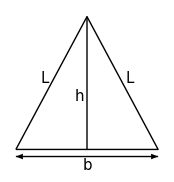
考虑底为 b = 16，腰为 L = 17 的等腰三角形。
		-Graphics-
使用毕达哥拉斯定理，我们可以求出三角形的高是 h=√(17^2-8^2)=15，恰好比底长小 1。
当 b = 272 而 L = 305 时，可以算出 h = 273，恰好比底长大 1，而且这是满足性质 h=b±1 的三角形中第二小的。
对于最小的 12 个满足 h=b±1 且 b,L 均为正整数的等腰三角形，求 ∑L。

```mathematica
With[{f=PellFunction[5,-1]},
    Sum[Last@f[n],{n,2,13}]
]
```

1118049290473932

令 x=b/2，由 x^2+(2x±1)^2=L^2 展开并整理后得到佩尔方程 (5x±2)^2-5 L^2=-1.

#### 139 毕达哥拉斯地砖

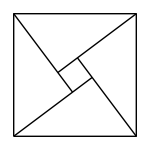
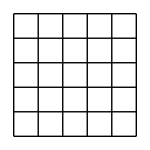
用 (a,b,c) 表示边长为整数的直角三角形的三边，可以将四个这样的三角形放在一起，使其外框构成边长为 c 的正方形。例如，边长为 (3, 4, 5) 的三角形可以构成一个 5 × 5 的正方形，中间留有一个 1 × 1 的洞。而这个 5 × 5 的正方形又恰好可以用 25 个 1 × 1 的小正方形组成。
		-Graphics-		-Graphics-
然而，如果我们用 (5, 12, 13) 的三角形，则中间的洞将会是 7 × 7 大小，不能用来组成 13 × 13 的大正方形。
考虑边长小于一亿的直角三角形，有多少个毕达哥拉斯三角形可以用中间留下的空洞大小的地砖恰好铺满外围的大正方形？

```mathematica
With[{LIMIT=10^8},
    ParallelSum[If[GCD[m,n]≠1,0,
        With[{a=m^2-n^2,b=2m n,c=m^2+n^2},
            If[Divisible[c,a-b],Floor[LIMIT/(a+b+c)],0]]],
        {m,2,Sqrt[LIMIT/2]},
        {n,BitAnd[m,1]+1,Min[m-1,LIMIT/(2m)-m],2}]
]//Timed
```

10057761
Time: 8.12158

```mathematica
JavaSolve[139,10^8]//Timed
```

10057761
Time: 0.470172

```mathematica
Module[{p,LIMIT=10^8},
    p[a_,b_,x_]:=
        If[a≥LIMIT,x,p[b,6b-a,x+Floor[LIMIT/a]]];
    p[12,70,0]
]//Timed
```

10057761
Time: 0.000088

符合条件的毕达哥拉斯三角形周长满足以下递归公式（未证明）：
	p(n)=6p(n-1)-p(n-2)
p(0)=12
p(1)=70

#### 140 修正斐波那契金块

考虑无穷级数 A_G(x)=x G_1+x^2 G_2+x^3 G_3+...，其中 G_k 是二阶递归关系 G_k=G_(k-1)+G_(k-2) 的第k项，其中 G_1 = 1，G_2 = 4，该序列为 1, 4, 5, 9, 14, 23, ...。在这个问题中，我们感兴趣的是那些使得 A_G(x) 为正整数的 x。对应于前五个自然数的 x 如下所示。
		x | A_F(x)
√2-1 | 1
1/2 | 2
(√13-2)/3 | 3
(√89-5)/8 | 4
(√34-3)/5 | 5
当 x 是有理数时，我们称 A_G(x) 是一个修正斐波那契金块，因为这样的数将会变得越来越稀少，例如，第 20 个修正斐波那契金块将是 211345365。
求前 30 个修正斐波那契金块的和。

```mathematica
Block[{n,y},
    With[{sol=Solve[5n^2+14n+1==y^2&&n>0&&y>0,Integers]},
        Total@Take[
            Union@Flatten@Table[
                Map[Simplify[n/.#]&]@(sol/.C[1]->i),
                {i,0,10}],
            30]]
]
```

5673835352990

同第 137 题，只是生成函数成为

g(x)=∑_(n=1)^∞ x^n(3 L_n-F_n)/2=(3 x^2+x)/(1-x-x^2)

其中 L_n 是卢卡斯数。

#### 141 累进平方数n的研究

正整数 n 被 d 除的商和余数分别是 q 和 r，除此之外，d,q,r 恰好是一个等比数列中的连续三个正整数项，但其对应顺序不一定一致。例如，58 被 6 除商 9 余 4，可以发现 4, 6, 9 构成等比数列的连续三项，公比是 3 / 2。我们称这样的数 n 为累进数。有些累进数，例如 9 或者 10404 = 102^2，恰好也是完全平方数。所有小于十万的累进平方数的和是 124657。
求所有小于一万亿（10^12）的累进平方数之和。

```mathematica
JavaSolve[141,10^12]//Timed
```

878454337159
Time: 4.54999

public class Problem141 {
    private final static long LIMIT = 1_000_000_000_000L;

    private static boolean isSquare(long n) {
        long r = (long)Math.sqrt(n);
        return r * r == n;
    }

    private static long gcd(long a, long b) {
        while (b != 0) {
            long m = a % b;
            a = b;
            b = m;
        }
        return a;
    }

    public long solve() {
        long sum = 0;
        for (long a = 2; a <= 10000; a++) {
            for (long b = 1; b < a; b++) {
                if (gcd(a, b) != 1)
                    continue;
                for (long c = 1; c < LIMIT; c++) {
                    long n = a*a*a*b*c*c + b*b*c;
                    if (n > LIMIT)
                        break;
                    if (isSquare(n))
                        sum += n;
                }
            }
        }
        return sum;
    }

    public static void main(String[] args) {
        System.out.println(new Problem141().solve());
    }
}

假设 r<d≤q 且公比为 a/b，其中 a,b 互质，则有

d=(a r)/b
q=(a^2 r)/b^2

因此 r 必须能够被 b^2 整除，如果设 r=c b^2，则

d=a b c
q=a^2 c
n=d q+r=a^3 b c^2+b^2 c

取以下迭代参数可缩小搜索范围

2≤a≤10000
1≤b<a 且 a,b 互质
1≤c 且 a^3 b c^2+b^2 c<10^12

#### 142 完全平方数收集

找出最小的 x+y+z 的值，其中正整数 x>y>z>0 满足 x+y, x-y, x+z, x-z, y+z, y-z 均为完全平方数。

```mathematica
JavaSolve[142]
```

1006193

#### 144 一束激光多次反射的研究

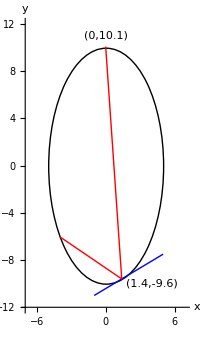
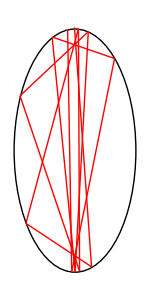
在激光物理学中，.93白腔.94指的是一个使激光束发生延迟的镜面系统。激光进入镜面系统后，最终会不断反射并重新射出。在本题中考察的白腔系统是一个椭圆，其方程为 4 x^2+y^2=100。在椭圆顶端割去了 -0.01≤x≤+0.01 的区域，使得激光能够进入和离开白腔。
		-Graphics-		-Graphics-
本题中，激光从白腔外的点 (0.0, 10.1) 发出，首次接触镜面的位置是 (1.4, -9.6)。每当激光击中椭圆表面时，它遵循反射定律“入射角等于反射角”，也就是说，入射光线和反射光线在入射点和法线的夹角相等。在左图中，红线表示的是激光前两次击中镜面的过程；蓝线表示的是激光第一次击中镜面时入射点的切线。右图展现了激光束前十次反射的路径。
对于椭圆的任意点 (x,y)，其切线的斜率 m 满足：m=-4x/y。法线是垂直于入射点的切线。
在激光离开白腔之前，它在椭圆的内表面上击中了多少次？

```mathematica
Module[{reflection,intersection,iterate},
    reflection[{{x1_,y1_},{x2_,y2_}}]:=
        With[{n={-4x2,-y2}/Sqrt[(4x2)^2+y2^2],r={x2-x1,y2-y1}},
            With[{s=Divide@@Reverse[r-2n(r.n)]},
                {{x2,y2},intersection[x2,y2,s]}]];
    
    intersection[x1_,y1_,s_]:=
        With[{x2=((s^2-4)x1-2s y1)/(s^2+4)},
          {x2,s(x2-x1)+y1}];
          
    iterate[coord:{_,{x_,y_}},step_]:=
        If[-0.01≤x≤0.01&&y>0,step,iterate[reflection[coord],step+1]];
    iterate[{{0,10.1},{1.4,-9.6}},0]
]
```

354

参考 Calculating reflected ray，可得到光反射方程为

R_r=R_i-2N(R_i ·N)

其中 N 是单位法线向量，R_i 是入射光线向量，R_r 是反射光线向量。
从点 (x_1,y_1) 出发，斜率为 s 的光线的方程可表述为

y_2=s(x_2-x_1)+y_1

光线与椭圆 4 x^2+y^2=100 相交的第一个点满足 4 x_1^2+y_1^2=100，代入 (1) 式得到与椭圆相交的第二个点：

4 x_2^2+(s(x_2-x_1)+y_1)^2=4 x_1^2+y_1^2=100

经过化简后最终得到

x_2=((s^2-4)x_1-2s y_1)/(s^2+4)

再由 (1) 式可求的 y_2。

#### 145 有多少小于十亿的可逆数？

有些正整数 n 满足这样一种性质，将它的数字逆序排列后和本身相加所得到的和 [n+reverse(n)] 的十进制表示只包含有奇数数字。例如，36 + 63 = 99 以及 409 + 904 = 1313。我们称这样的数是可逆的；因此 36, 63, 409 和 904 都是可逆的。无论是 n 还是 reverse(n) 都不允许出现前导 0。
在小于一千的数中，一共有 120 个可逆数。
在小于十亿（10^9）的数中，一共有多少个可逆数？

```mathematica
Module[{a},
    a[n_?EvenQ]:=20 30^(n/2-1);
    a[n_/;Divisible[n-1,4]]:=0;
    a[n_/;Divisible[n-3,4]]:=100 500^((n-3)/4);
    Sum[a[n],{n,1,9}]
]
```

608720

经过枚举可知，对一个数字对 (a,b)，
    a) 如果 a+b 是奇数且 a+b>10，有 20 种选择方式；
    b) 如果 a+b 是奇数且 a+b<10，当允许 0 时有 30 种选择方式，不允许 0 时有 20 种选择方式；
    c) 如果 a+b 是偶数且 a+b>10，有 25 种选择方式；
    d) 如果 a+b 是偶数且 a+b<10，有 25 种选择方式。
对一个 n 位数，通过以下条件判断其是否可逆：
    a) 如果 n=2k，则所有位都不能进位，因此所有的数字对之和必须是奇数且小于 10，而且不允许前导 0，这样的数字对有 20×30^(k-1) 种选择方式；
    b) 如果 n=4k+1，则没有这样的数能够满足条件；
    c) 如果 n=4k+3，由于最中间的数字是自身相加为偶数，因此必须借位。其两边是一对相加为奇数且和大于 10 的数字，再向外是一对相加为偶数且和小于 10 的数字，依次类推。最外边的一对数字相加为奇数且和大于 10，最中间的数字必须小于 5，这样共有 5 20 25^k 20^k=100 500^k 种选择方式。

#### 146 素数模式研究

使得 n^2+1, n^2+3, n^2+7, n^2+9, n^2+13 以及 n^2+27 均为素数的最小的 n 是 10。所有小于一百万的数中，满足这一条件的所有整数 n 的和为 1242490。
在小于一亿五千万的数中，所有满足这一条件的正整数 n 的和是多少？

```mathematica
ParallelSum[
    If[!Divisible[n,3]&&Mod[n+2,7]≥5&&
            With[{m=n^2},
                PrimeQ[m+1]&&
                NextPrime[m+1]==m+3&&
                NextPrime[m+3]==m+7&&
                NextPrime[m+7]==m+9&&
                NextPrime[m+9]==m+13&&
                NextPrime[m+13]==m+27],
        n,0],
    {n,10,150 10^6,10}]//Timed
```

676333270
Time: 11.9076

#### 148 探索帕斯卡三角

可以验证，帕斯卡三角的前 7 行没有一个整数能够被 7 整除：
		1
1 |  1
1 |  2 |  1
1 |  3 |  3 |  1
1 |  4 |  6 |  4 |  1
1 |  5 | 10 | 10 |  5 |  1
1 |  6 | 15 | 20 | 15 |  6 |  1
然而，如果我们检查前一百行就会发现，在这 5050 个数上，只有 2361 个不能被 7 整除。
找出帕斯卡三角前十亿（10^9）行中不能被 7 整除的数的数目。

```mathematica
Module[{f},
    f[p_?PrimeQ,n_]:=f[IntegerDigits[n,p],p(p+1)/2,1/2,0];
    f[{},_,_,r_]:=r;
    f[{xs___,x_},d_,m_,r_]:=f[{xs},d,d m,(x+1)(m x+r)];
    f[7,10^9]
]
```

2129970655314432

#### 149 寻找最大和子序列

观察下面的表格，很容易发现，在所有同一横行、竖列或对角线的任意数量相邻数之和中，最大值是 16 ( = 8 + 7 + 1)。
				-2 | 5 | 3 | 2
9 | -6 | 5 | 1
3 | 2 | 7 | 3
-1 | 8 | -4 | 8
现在，让我们再来找一次，不过是在一个更大尺寸的表格中。
首先，使用现在被称为“延迟斐波那契生成器”的方法，生成四百万个伪随机数：
	对于 1≤k<=55,s_k=[100003-200003k+300007 k^3] (mod 1000000) - 500000。
	对于 5≤k<=4000000,s_k=[s_(k-24)+s_(k-55)+1000000] (mod 1000000) - 500000。
如此一来，可以得到 s_10 = -393027，而 s_100 = 86613。
这些 s 的项随后被填入一个 2000 × 2000的表格，前 2000 个数字按顺序填入第一行，然后 2000 个数字在第二行，依此类推。
最后，求所有同一横行、竖列或对角线的任意数量相邻数之和的最大值。

```mathematica
JavaSolve[149,2000]//Timed
```

52852124
Time: 0.059674

#### 154 探索帕斯卡四面体

我们用球构建一个三角形四面体，每一个球的下一层都由恰好三个球支撑。
		-Graphics-
然后，我们计算从顶端到每一个位置的路径数：每一条路径从顶端出发，然后每次都走向下一层支撑当前位置的球的三个球之一。最终，到达每个位置的路径数是它上方的球的路径数之和（根据位置的不同，每个位置的上方最多可能有三个球）。最终的结果被称为帕斯卡四面体，这个四面体第 n 层的结果将是三项式 (x+y+z)^n 的系数。
在三项式 (x+y+z)^20000 的展开式中，有多少个系数是 10^12 的倍数？

```mathematica
JavaSolve[154]//Timed
```

479742450
Time: 35.0118

#### 155 电容电路计算

考虑如下电路，其中使用的电容都是完全相同的值 C。电容之间互相串联构成次级单元，然后次级单元之间互相串联或和其它次级单元或电容并联构成更大的次级单元，最终组成整个电路。
使用 n 个电容并重复这个简单的过程，我们可以构建出一系列总电容不同的电路。例如，使用最多 n = 3 个值为 60μF 的电容，我们可以得到 7 种不同的总电容：
		-Graphics-
我们用 D(n) 表示当我们使用最多 n 个相同的电容并重复上述简单过程后，我们能够得到的总电容的种数，我们有：D(1)=1, D(2)=3, D(3)=7...
求 D(18)。
提醒：当电容 C_1, C_2 等等并联时，总电容为：C_T=C_1+C_2+...，而当它们串联时，总电容为：1/C_T=1/C_1+1/C_2+...。

```mathematica
JavaSolve[155,18]//Timed
```

3857447
Time: 7.13882

#### 156 数字计数

从零开始的自然数在十进制中如下表示：
	0 1 2 3 4 5 6 7 8 9 10 11 12 ...
考虑数字 d = 1。当我们写下数 n 之后，我们计算一下到目前为止数字 1 出现的次数，并记为 f(n,1)。f(n,1) 的前面一部分值如下所示：
		n | f(n,1)
0 | 0
1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 2
11 | 4
12 | 5
注意到 f(n,1) 从不等于3。等式 f(n,1)=n 的前两个解是 n = 0 和 n = 1，下一个解是 n = 199981。
同样地我们记 f(n,d) 表示在写下 n 之后 d 出现的次数。事实上，对于任意一个数字 d ≠ 0，0 都是方程 f(n,d)=n 的第一个解。
记 s(d) 是所有 f(n,d)=n 的解的和。已知 s(1) = 22786974071。
对于 1 ≤ d ≤ 9，求 ∑s(d)。
注意：如果对于某些 n，对于多于一个的 d 均满足 f(n,d)=n，这个数 n 对于每个 d 都要计算一遍。

```mathematica
Module[{f,s},
    f[n_,d_]:=
        ∑_(r=0)^Log10[n] (10^r(1+⌊(n-10^r d)/10^(r+1)⌋)+If[Mod[⌊n/10^r⌋,10]==d,Mod[n,10^r]+1-10^r,0]);
    
    s[1]=22786974071;
    s[d_]:=s[d,1,10^10 d(d-1)/2];
    s[d_,n_,S_]:=S/;n≥10^10;
    s[d_,n_,S_]:=
        With[{c=Abs[f[n,d]-n]},
            If[c==0,
                s[d,n+1,S+d(n+10^10(d-1)/2)],
                s[d,n+Ceiling[c/10],S]]];
    
    Block[{$IterationLimit=Infinity},Sum[s[d],{d,1,9}]]
]//Timed
```

21295121502550
Time: 3.98769

#### 162 十六进制数

十六进制数系统使用16个不同的数字：
	0, 1, 2, 3, 4, 5, 6, 7, 8, 9, A, B, C, D, E, F
十六进制数 AF 在十进制下等于 10 × 16 + 15 = 175。
三位十六进制数 10A, 1A0, A10 和 A01 都包含数字 0, 1 和 A。和十进制下一样，在十六进制中没有前导零。
有多少至多十六位的十六进制数同时包含 0, 1 和 A？用十六进制数表示你的答案。
（A, B, C, D, E 和 F均为大写字母，没有前导零或末尾标识符来表明该数字为十六进制，例如，1A3F 不能写成 1a3f 或 0x1a3f 或 $1A3F 或 #1A3F 或0000001A3F）

```mathematica
Module[{f},
    f[digits_]:=f[digits,False,False,False,False];
    f[0,True,True,True,_]=1;
    f[0,_,_,_,_]=0;
    f[digits_,zero_,one_,ten_,any_]:=
        With[{next=f[digits-1,zero,one,ten,True]},
            13*next+
            If[zero,next,f[digits-1,any,one,ten,any]]+
            If[one,next,f[digits-1,zero,True,ten,True]]+
            If[ten,next,f[digits-1,zero,one,True,True]]];
    f[16]~IntegerString~16//ToUpperCase
]
```

3D58725572C62302

#### 165 交点

一条线段由其两个端点唯一决定。考虑平面几何中的两条线段，一共有如下三种可能性：两条线段没有、有一个或者有无数个交点。进一步地，当两条线段恰好有一个交点时，可能这个交点是其中一条或两条的端点。如果这个交点不是任一条线段的端点，那它一定是这两条线段的内点。当两条线段 L1 和 L2 的交点 T 是这两条线段唯一的交点且是这两条线段的内点时，我们称 T 为这两条线段的真交点。
考虑以下三条线段 L_1, L_2 和 L_3：
	L_1: (27, 44) to (12, 32)
	L_2: (46, 53) to (17, 62)
	L_3: (46, 70) to (22, 40)
可以验证，线段  L_2 和  L_3 有一个真交点。注意到  L_3  的一个端点 (22, 40) 恰好在 L_1 上，因此这不是一个真交点。L_1 和 L_2 则没有交点。因此在这三条线段中，一共有一个真交点。
现在我们来对 5000 条线段求真交点数。首先，我们用“布鲁姆-布鲁姆-舒布”伪随机数生成算法生成 20000 个数。
	s_0=290797
s_(n+1)=s_n×s_n (mod 50515093)
t_n=s_n (mod 500)
为了生成每一条线段，我们使用 t_n 的连续四项，也就是说，第一条线段是 (t_1,t_2) 至 (t_3,t_4)。由上述算法生成的前四个数是：27, 144, 12 和 232，因此第一条线段是 (27, 144) 至 (12, 232)。
在这 5000 条线段中，有多少个真交点？

```mathematica
JavaSolve[165,5000]//Timed
```

2868889
Time: 1.07613

#### 187 半素数

合数是指包含至少两个质因数的整数。例如，15 = 3 × 5; 9 = 3 × 3; 12 = 2 × 2 × 3。
在小于 30 的合数中，有十个合数包含恰好两个不一定不同的质因数：4, 6, 9, 10, 14, 15, 21, 22, 25, 26。
在小于 10^8 的合数中，有多少个包含恰好两个不一定不同的质因数？

```mathematica
With[{n=10^8},
    Plus@@Map[PrimePi[n/#]-PrimePi[#]+1&]@Prime@Range@PrimePi@Sqrt[n]
]
```

17427258

#### 206 被遮挡的平方数

找出唯一一个其平方形如 1_2_3_4_5_6_7_8_9_0, 的正整数，其中每个 “_” 表示一位数字。

```mathematica
Module[{lbound,ubound,pattern},
    lbound=Floor[Sqrt[1020304050607080900]/100]*100+70;
    ubound=Floor[Sqrt[1929394959697989990]/100]*100+70;
    pattern=Range[9]~Append~0~Riffle~_;
    SelectFirst[MatchQ[IntegerDigits[#^2],pattern]&]@Range[ubound,lbound,-100]
]
```

1389019170

#### 235 等差比数列

已知等差比数列 u(k)=(900-3k)r^(k-1)，记 s(n)=∑_(k=1)^n u(k).
求使得 s(5000)=-600000000000 的 r 值。
将你的答案四舍五入至小数点后 12 位小数。

```mathematica
Module[{f,r},
    f[n_,r_]:=Sum[(900-3k)r^(k-1),{k,1,n}]+6*^11;
    NumberForm[r/.FindRoot[f[5000,r],{r,1.0},WorkingPrecision->20],{Infinity,12}]
]
```

1.002322108633

#### 243 不可约度

分子小于分母的正分数被称为真分数。对于分母 d，一共有 d-1 个真分数；例如，当 d = 12 时为：
	1/12,2/12,3/12,4/12,5/12,6/12,7/12,8/12,9/12,10/12,11/12
我们称不能被约简的分数为不可约分数。进一步地，我们可以定义分母的不可约度 R(d) 为它的真分数中不可约分数的比例；例如，R(12) = 4 / 11。事实上，d = 12 是不可约度 R(d)<4/10 的最小分母。
求不可约度 R(d)  < 15499 / 94744 的最小分母 d。

```mathematica
Module[{R,findInRange,find},
    R[n_]:=EulerPhi[n]/(n-1);
    findInRange[i_,f_]:=
        With[{step=Times@@Prime[Range[i]]},
            NestWhile[#+step&,step,R[#]≥f&,1,Prime[i+1]-1]];
    find[f_]:=
        Do[With[{d=findInRange[i,f]},If[R[d]<f,Return[d]]],{i,1,Infinity}];
    find[15499/94744]
]
```

892371480

#### 345 矩阵和

在一个矩阵中选择部分元素，使得每个元素都是所在的行和列中唯一被选中的元素，这些元素的和的最大值定义为矩阵的矩阵和。例如，如下矩阵的矩阵和为 3315 ( = 863 + 383 + 343 + 959 + 767)：
		7 | 53 | 183 | 439 | 863
497 | 383 | 563 | 79 | 973
287 | 63 | 343 | 169 | 583
627 | 343 | 773 | 959 | 943
767 | 473 | 103 | 699 | 303

求如下矩阵的矩阵和：

```mathematica
Module[{matrix},
    matrix=({{7, 53, 183, 439, 863, 497, 383, 563, 79, 973, 287, 63, 343, 169, 583}, {627, 343, 773, 959, 943, 767, 473, 103, 699, 303, 957, 703, 583, 639, 913}, {447, 283, 463, 29, 23, 487, 463, 993, 119, 883, 327, 493, 423, 159, 743}, {217, 623, 3, 399, 853, 407, 103, 983, 89, 463, 290, 516, 212, 462, 350}, {960, 376, 682, 962, 300, 780, 486, 502, 912, 800, 250, 346, 172, 812, 350}, {870, 456, 192, 162, 593, 473, 915, 45, 989, 873, 823, 965, 425, 329, 803}, {973, 965, 905, 919, 133, 673, 665, 235, 509, 613, 673, 815, 165, 992, 326}, {322, 148, 972, 962, 286, 255, 941, 541, 265, 323, 925, 281, 601, 95, 973}, {445, 721, 11, 525, 473, 65, 511, 164, 138, 672, 18, 428, 154, 448, 848}, {414, 456, 310, 312, 798, 104, 566, 520, 302, 248, 694, 976, 430, 392, 198}, {184, 829, 373, 181, 631, 101, 969, 613, 840, 740, 778, 458, 284, 760, 390}, {821, 461, 843, 513, 17, 901, 711, 993, 293, 157, 274, 94, 192, 156, 574}, {34, 124, 4, 878, 450, 476, 712, 914, 838, 669, 875, 299, 823, 329, 699}, {815, 559, 813, 459, 522, 788, 168, 586, 966, 232, 308, 833, 251, 631, 107}, {813, 883, 451, 509, 615, 77, 281, 613, 459, 205, 380, 274, 302, 35, 805}});
    Total@Map[matrix⟦Sequence@@#⟧&]@Hungarian[-matrix]
]
```

13938

#### 347 能被两个素数整除的最大整数

在不大于 100 的正整数中，只能被 2 和 3 整除的最大整数是 96，因为 96 =  32 × 3 = 2^5 × 3。对于两个不同的素数 p 和 q，在不大于 N 的正整数中，只能被 p 和 q 整除的最大整数记为 M(p,q,N)；如果这样的正整数不存在，则记 M(p,q,N)=0。
例如，M(2, 3, 100) = 96。M(3, 5, 100) = 75 而非 90，因为 90 能被 2, 3, 5 整除。此外 M(2 ,73, 100) = 0，因为不存在不大于 100 的正整数只能被 2 和 73 整除。
记 S(N) 为所有不同的 M(p,q,N) 之和。已知 S(100) = 2262。
求 S(10 000 000)。

```mathematica
With[{limit=10^7},
    Total@Map[Max@Map[First,#]&]@GroupBy[Last]@
        ParallelTable[
            With[{factors=FactorInteger[n]},
                If[Length[factors]==2,
                    {n,First/@factors},
                    Nothing]],
            {n,Floor@Sqrt[limit],limit}]
]//Timed
```

11109800204052
Time: 25.9517

```mathematica
JavaSolve[347,10^7]//Timed
```

11109800204052
Time: 5.7165

#### 348 平方数和立方数之和

许多数可以表示称一个平方数和一个立方数之和，有些数甚至有不止一种表示方式。考虑能表示成大于 1 的平方数和立方数之和，且恰好有 4 种不同的表示方式的回文数。例如，5229225 是一个回文数，而且它恰好可以用 4 种不同的方式进行表达：
	2285^2 + 20^3
	2223^2 + 66^3
	1810^2+ 125^3
	1197^2 + 156^3
求出这类回文数中最小的五个之和。

```mathematica
Total@JavaSolve[348,5]
```

1004195061

#### 357 生成素数的整数

考虑 30 的约数：1, 2, 3, 5, 6, 10, 15, 30。可以看出，对于 30 的每个约数 d，d+30/d 都是素数。
存在不超过 100000000 的正整数 n，使得对于 n 的每个约数 d，d+n/d 都是素数；求所有这样的数 n 的和。

```mathematica
Module[{check},
    check[n_]:=AllTrue[PrimeQ[#+n/#]&]@Divisors[n];
    ParallelSum[With[{n=Prime[i]-1},
        If[check[n],n,0]],
        {i,1,PrimePi[10^8]}]
]//Timed
```

1739023853137
Time: 26.7618

```mathematica
JavaSolve[357,10^8]//Timed
```

1739023853137
Time: 1.67404

#### 387 哈沙德数

能够被其各位数字和整除的数被称为哈沙德数或奈文数。201 是一个哈沙德数，因为它能被 3 整除（其各位数字和是 3）。
如果我们截去 201 的最后一位数字，我们得到 20，同样是一个哈沙德数。如果我们截去 20 的最后一位数字，我们得到 2，仍然是一个哈沙德数。如果一个哈沙德数不断截去最后一位数字的结果始终是哈沙德数，我们称之为可右截哈沙德数。
此外：201 / 3 = 67 是一个素数。如果一个哈沙德数被其各位数字除的结果是一个素数，我们称之为强哈沙德数。
现在我们取素数 2011。如果我们截去 2011 的最后一位数字，我们得到 201，一个可右截的强哈沙德数。我们称这样的素数为可右截强哈沙德素数。
已知所有小于 10000 的可右截强哈沙德素数之和为 90619。
求所有小于 10^14 的可右截强哈沙德素数之和。

```mathematica
Module[{HarshadQ,StrongHarshadQ,iterate},
    HarshadQ[n_]:=Divisible[n,Plus@@IntegerDigits[n]];
    StrongHarshadQ[n_]:=PrimeQ[n/Plus@@IntegerDigits[n]];
    
    iterate[{total_,{harshads_}}]:=
        Reap@Fold[With[{h=#2},
            Fold[With[{n=10h+#2},
                If[HarshadQ[n],Sow[n]];
                If[PrimeQ[n]&&StrongHarshadQ@Floor[n/10],#1+n,#1]]&,
            #1,Range[0,9]]]&,
        total,harshads];
    
    First@Nest[iterate,{0,{Range[9]}},13]
]
```

696067597313468

#### 493 彩虹之下

在容器中装有 70 个球，分别染上彩虹的七种颜色，每种颜色各有 10 个。
从容器中随机取出 20 个球，这些球中不同颜色的数量的期望值是多少？
你的答案应当保留到小数点后 9 位小数（a.bcdefghij）。

```mathematica
N[7(1-Binomial[60,20]/Binomial[70,20]),10]
```

6.818741802

#### 500 第500题!!!

120 的因数数目为 16。事实上 120 是最小的有 16 个因数的数。
找出最小的有 2^500500 个因数的数。
给出这个数除以 500500507 的余数。

```mathematica
Module[{iter,LIMIT=500500,MODULO=500500507},
    iter[i_,t_]:=
        With[{len=PrimePi[Prime[LIMIT]^(1/i)]},
            If[len==0,
                Union[t,Prime[Range[LIMIT-Length[t]]]],
                iter[i*2,Union[t,Prime[Range[len]]^i]]]];
    Fold[Mod[#1 #2,MODULO]&,1,iter[2,{}]]
]
```

35407281

#### 531 中国剩余定理

记 g(a,n,b,m) 为以下方程组的最小非负解：
	x≡a (mod n)
	x≡b (mod m)
如果解不存在，则该函数记为 0。例如，g(2,4,4,6)=10，但 g(3,4,4,6)=0。
记 φ(n) 为欧拉总计函数。
记 f(n,m)=g(φ(n),n,φ(m),m)。
对于 1000000≤n<m<1005000，求 ∑f(n,m)。

```mathematica
JavaSolve[531,1000000,1005000]//Timed
```

4515432351156203105
Time: 2.79736

#### 549 阶乘的整除性

使 m! 能被 10 整除的最小的 m 为 5。使 m! 能被 25 整除的最小的 m 为 10。
记使 m! 能被 n 整除的最小的 m 为 s(n)。因此 s(10)=5，s(25)=10。
记 S(n) 为 ∑s(i)，其中 2≤i≤n。已知 S(100)=2012。
求 S(10^8)。

```mathematica
Module[{s,kempner,LIMIT=10^8},
    s[n_?PrimeQ]:=n;
    s[n_]:=Max[kempner@@@FactorInteger[n]];
    
    kempner[p_,1]:=p;
    kempner[p_,a_]:=p*a/;a≤p;
    kempner[p_,a_]:=kempner[p,a]=
        kempner[p,a,{0,a},Floor@Log[p,1+a(p-1)],0];
    
    kempner[p_,a_,{k_,0},_,s_]:=a(p-1)+s+k;
    kempner[p_,a_,{k_,r_},v_,s_]:=
        With[{av=(p^v-1)/(p-1)},
            kempner[p,a,QuotientRemainder[r,av],v-1,s+k]];
    
    ParallelSum[s[n],{n,2,LIMIT}]
]//Timed
```

476001479068717
Time: 189.257

参考: Smarandache Function

#### 615 第一百万个拥有至少一百万个质因数的数

考虑所有拥有至少 5 个质因数的自然数，这些质因数不必完全不同。将这些数按从小到大排序，所构成的列表开头是这几个数：
	32 = 2 · 2 ⋅ 2 ⋅ 2 ⋅ 2
	48 = 2 ⋅ 2 ⋅ 2 ⋅ 2 ⋅ 3
	64 = 2 ⋅ 2 ⋅ 2 ⋅ 2 ⋅ 2 ⋅ 2
	72 = 2 ⋅ 2 ⋅ 2 ⋅ 3 ⋅ 3
	80 = 2 ⋅ 2 ⋅ 2 ⋅ 2 ⋅ 5
	96 = 2 ⋅ 2 ⋅ 2 ⋅ 2 ⋅ 2 ⋅ 3
所以，第五个拥有至少 5 个质因数的数是 80。
找出第一百万个拥有至少一百万个质因数的数。将你的答案对 123454321 取余。

```mathematica
JavaSolve[615,10^6,123454321]//Timed
```

108424772
Time: 12.3704

#### 624 Two heads are better than one

An unbiased coin is tossed repeatedly until two consecutive heads are obtained. Suppose these occur on the (M-1) th and Mth toss. Let P(n) be the probability that M is divisible by n. For example, the outcomes HH, HTHH, THTTHH all count towards P(2), but THH and HTTHH do not.
You are given that P(2)=3/5 and P(3)=9/31. Indeed, it can be shown that P(n) is always a rational number.
For a prime p and a fully reduced fraction a/b, define Q(a/b,p) to be the smallest positive q for which a≡b q (mod p). For example Q(P(2),109)=Q(3/5,109)=66, because 5×66=330≡3 (mod 109) and 66 is the smallest positive such number. Similarly Q(P(3),109)=46.
Find Q(P(10^18),1000000009).

```mathematica
Module[{m,n,m5,Q},
    n=10^18;
    m=10^9+9;
    m5=PowerMod[5,1/2,m];
    Q[a_,b_,p_]:=Mod[a*PowerMod[b,-1,p],p];
    Mod[
        Q[2,m5,m]*(
            Q[PowerMod[1+m5,n-1,m],PowerMod[4,n,m]-PowerMod[1+m5,n,m],m]-
            Q[PowerMod[1-m5,n-1,m],PowerMod[4,n,m]-PowerMod[1-m5,n,m],m]),
        m]
]
```

984524441

Out of all 2^n sequences of n coin tosses, F_(n-1) finish with two heads and do not contain two consecutive heads before the end, so

P(n)=∑_(k=1)^∞ (F_(kn-1))/2^kn

Let α=1+√5, β=1-√5, then

F_n=(α^n-β^n)/(2^n √5)

so

P(n)=2/(α √5)∑_(k=1)^∞ (α/4)^kn-2/(β √5)∑_(k=1)^∞ (β/4)^kn
=2/(α √5)(α/4)^n/(1-(α/4)^n)-2/(β √5)(β/4)^n/(1-(β/4)^n)
=2/(√5)(α^(n-1)/(4^n-α^n)-β^(n-1)/(4^n-β^n))

```mathematica
Module[{an,a0,bn,b0,a,b,n=10^18,m=10^9+9},
    an={{0,1,0},{0,0,1},{4,6,1}};
    a0={1,3,9};
    bn={{0,1,0,0},{0,0,1,0},{0,0,0,1},{-16,-20,2,5}};
    b0={1,5,31,145};
    a=Last@MatrixPowerMod[an,n-3,m].a0;
    b=Last@MatrixPowerMod[bn,n-4,m].b0;
    Mod[a*PowerMod[b,-1,m],m]
]
```

984524441

The recurrence of the numerator of P(n) is

a_n=a_(n-1)+6 a_(n-2)+4 a_(n-3)
a_1=1,a_2=3,a_3=9

The recurrence of the denominator of P(n) is

b_n=5 b_(n-1)+2 b_(n-2)-20 b_(n-3)-16 b_(n-4)
b_1=1,b_2=5,b_3=31,b_4=145

#### 公共函数

```mathematica
Needs["Euler`"]
```